# Eccentricity Reduction

## Version 1.0.0

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

## File Select

```mathematica
(*Time Step, Time, XYZ position of BH1, XYZ position of BH2*)
(*Reading in any dgr_BHLocations.dat file output from Dendro should work in this format*)
{ts,tList,BHX1,BHY1,BHZ1,BHX2,BHY2,BHZ2}=Transpose@Drop[Import["C:\\Users\\natha\\Documents\\School\\Research\\Hirschmann\\SupercomputerOutput\\GR\\expanse\\q1_long_eta_medium\\datfiles\\dgr_BHLocations.dat"],1];
```

## Equations of Motion

```mathematica
<<"DifferentialEquations`InterpolatingFunctionAnatomy`"
```

### Eccentricity Reduction 3.5PN formulas

#### Formulas for λt, pr, pt, px, py

```mathematica
δrmas[Amp_,R0_,Ω0_,q_,γ_]:=(Amp R0)/(2 Ω0)-(3 Amp (3+7 q+3 q^2) γ)/(4 (1+q)^2 Ω0)
```

```mathematica
λt1PNLin[ecc_,sign_,R0_,η_]:=1+(sign*Abs[ecc])/2+sign*Abs[ecc] (-1/R0-η/(2 R0))
```

```mathematica
pr[x_,y_,Px_,Py_]:=(Px x+Py y)/(√(x^2+y^2))
pθ[x_,y_,Px_,Py_]:=x Py -y Px
pt[x_,y_,Px_,Py_]:=(x Py -y Px)/(√(x^2+y^2))
Px[x_,y_,Pr_,Pt_]:=-(-Pr x+Pt y)/(√(x^2+y^2));
Py[x_,y_,Pr_,Pt_]:=-(-Pt x-Pr y)/(√(x^2+y^2));
```

```mathematica
solspxpy=Flatten@Solve[{pr[x,y,px,py]==Pr,pt[x,y,px,py]==Pt},{px,py}]
```

{px→-(-Pr x+Pt y)/(√(x^2+y^2)),py→-(-Pt x-Pr y)/(√(x^2+y^2))}

We write two small functions for given Pr and Pt -> Px and Py and viceversa.

```mathematica
PxPyToPrPt[x_,y_,Px_,Py_]:=Module[{Pr ,Pt },
Pr=pr[x,y,Px,Py];
Pt=pt[x,y,Px,Py];
{Pr,Pt}
]
```

```mathematica
PrPtToPxPy[x_,y_,Pr_,Pt_]:=Module[{px ,py },
px=Px[x,y,Pr,Pt];
py=Py[x,y,Pr,Pt];
{px,py}
]
```

```mathematica
λr1PNResSum[Amp_,ϕ_,Pr0_,Ω0_,R0_,η_,γ_]:=1+(Amp η Tan[ϕ])/(2 √R0 Ω0 Abs[Pr0] √(Sec[ϕ]^2))+(Amp γ η Tan[ϕ])/(2 R0^(3/2) Ω0 Abs[Pr0] √(Sec[ϕ]^2));
λt1PNResSum[Amp_,ϕ_,Ω0_,R0_,η_,γ_]:=1+Amp/(4 Ω0 √(Sec[ϕ]^2))-(Amp γ (1+3 η))/(8 R0 Ω0 √(Sec[ϕ]^2));
```

#### Formulas for Ω and Pt (3.5PN)

```mathematica
mωr35SPN[r_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
1/r^(3/2)*(1-((3+5 q+3 q^2) γ)/(2 (1+q)^2 r)+(γ^(3/2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^(3/2))+(3 γ^(5/2) (16 χ1z+30 q χ1z+34 q^2 χ1z+13 q^3 χ1z+13 q χ2z+34 q^2 χ2z+30 q^3 χ2z+16 q^4 χ2z))/(16 (1+q)^4 r^(5/2))+1/r^2 γ^2 ((24+103 q+164 q^2+103 q^3+24 q^4)/(16 (1+q)^4)-(3 χ1x^2)/(2 (1+q)^2)+(3 χ1y^2)/(4 (1+q)^2)+(3 χ1z^2)/(4 (1+q)^2)-(3 q χ1x χ2x)/(1+q)^2-(3 q^2 χ2x^2)/(2 (1+q)^2)+(3 q χ1y χ2y)/(2 (1+q)^2)+(3 q^2 χ2y^2)/(4 (1+q)^2)+(3 q χ1z χ2z)/(2 (1+q)^2)+(3 q^2 χ2z^2)/(4 (1+q)^2))+1/r^3 γ^3 ((167 π^2 q)/(128 (1+q)^2)-1/(96 (1+q)^6)(120+2744 q+10049 q^2+14820 q^3+10049 q^4+2744 q^5+120 q^6)+((76+180 q+155 q^2) χ1x^2)/(16 (1+q)^4)-((43+85 q+55 q^2) χ1y^2)/(8 (1+q)^4)-((28+124 q+135 q^2) χ1z^2)/(32 (1+q)^4)+(q (120+187 q+120 q^2) χ1x χ2x)/(8 (1+q)^4)+(q^2 (155+180 q+76 q^2) χ2x^2)/(16 (1+q)^4)-(q (54+95 q+54 q^2) χ1y χ2y)/(4 (1+q)^4)-(q^2 (55+85 q+43 q^2) χ2y^2)/(8 (1+q)^4)-(q (96+127 q+96 q^2) χ1z χ2z)/(16 (1+q)^4)-(q^2 (135+124 q+28 q^2) χ2z^2)/(32 (1+q)^4))+1/r^(7/2)γ^(7/2) (-(3 (4+q) χ1z^3)/(8 (1+q)^4)-(q (135+385 q+363 q^2+377 q^3+387 q^4+168 q^5) χ2z)/(32 (1+q)^6)-(9 q χ1z^2 χ2z)/(4 (1+q)^3)+(3 q^3 (1+4 q) χ2x^2 χ2z)/(2 (1+q)^4)-(3 q^3 (1+4 q) χ2y^2 χ2z)/(8 (1+q)^4)-(3 q^3 (1+4 q) χ2z^3)/(8 (1+q)^4)+χ1y^2 (-(3 (4+q) χ1z)/(8 (1+q)^4)-(9 q (1+2 q) χ2z)/(4 (1+q)^4))+χ1x^2 ((3 (4+q) χ1z)/(2 (1+q)^4)+(9 q (2+3 q) χ2z)/(4 (1+q)^4))+χ1x ((9 q (2+q) χ1z χ2x)/(4 (1+q)^4)+(9 q^2 (1+2 q) χ2x χ2z)/(4 (1+q)^4))+χ1y ((9 q^2 χ1z χ2y)/(4 (1+q)^4)+(9 q^2 χ2y χ2z)/(4 (1+q)^4))+χ1z (-(168+387 q+377 q^2+363 q^3+385 q^4+135 q^5)/(32 (1+q)^6)+(9 q^2 (3+2 q) χ2x^2)/(4 (1+q)^4)-(9 q^2 (2+q) χ2y^2)/(4 (1+q)^4)-(9 q^2 χ2z^2)/(4 (1+q)^3))))
]
```

```mathematica
Pt35SPN[r_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
q/((1+q)^2 √r)*(1+(2 γ)/r-(3 γ^(3/2) (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(4 (1+q)^2 r^(3/2))+(γ^(5/2) (-72 χ1z-116 q χ1z-60 q^2 χ1z-13 q^3 χ1z-13 q χ2z-60 q^2 χ2z-116 q^3 χ2z-72 q^4 χ2z))/(16 (1+q)^4 r^(5/2))+1/(16 (1+q)^2 r^2)γ^2 (42+41 q+42 q^2-24 χ1x^2+12 χ1y^2+12 χ1z^2-48 q χ1x χ2x-24 q^2 χ2x^2+24 q χ1y χ2y+12 q^2 χ2y^2+24 q χ1z χ2z+12 q^2 χ2z^2)+1/(128 (1+q)^4 r^3)γ^3 (480-2636 q+163 π^2 q-6128 q^2+326 π^2 q^2-2636 q^3+163 π^2 q^3+480 q^4-640 χ1x^2+472 q^2 χ1x^2-64 χ1y^2-640 q χ1y^2-512 q^2 χ1y^2+512 χ1z^2+224 q χ1z^2-108 q^2 χ1z^2+192 q χ1x χ2x+560 q^2 χ1x χ2x+192 q^3 χ1x χ2x+472 q^2 χ2x^2-640 q^4 χ2x^2-864 q χ1y χ2y-1856 q^2 χ1y χ2y-864 q^3 χ1y χ2y-512 q^2 χ2y^2-640 q^3 χ2y^2-64 q^4 χ2y^2+480 q χ1z χ2z+1064 q^2 χ1z χ2z+480 q^3 χ1z χ2z-108 q^2 χ2z^2+224 q^3 χ2z^2+512 q^4 χ2z^2)+1/r^(7/2)γ^(7/2) (-(5 (4+q) χ1z^3)/(8 (1+q)^4)-(q (103+145 q-27 q^2+252 q^3+670 q^4+348 q^5) χ2z)/(32 (1+q)^6)-(15 q χ1z^2 χ2z)/(4 (1+q)^3)+(5 q^3 (1+4 q) χ2x^2 χ2z)/(2 (1+q)^4)-(5 q^3 (1+4 q) χ2y^2 χ2z)/(8 (1+q)^4)-(5 q^3 (1+4 q) χ2z^3)/(8 (1+q)^4)+χ1y^2 (-(5 (4+q) χ1z)/(8 (1+q)^4)-(15 q (1+2 q) χ2z)/(4 (1+q)^4))+χ1x^2 ((5 (4+q) χ1z)/(2 (1+q)^4)+(15 q (2+3 q) χ2z)/(4 (1+q)^4))+χ1x ((15 q (2+q) χ1z χ2x)/(4 (1+q)^4)+(15 q^2 (1+2 q) χ2x χ2z)/(4 (1+q)^4))+χ1y ((15 q^2 χ1z χ2y)/(4 (1+q)^4)+(15 q^2 χ2y χ2z)/(4 (1+q)^4))+χ1z (-(348+670 q+252 q^2-27 q^3+145 q^4+103 q^5)/(32 (1+q)^6)+(15 q^2 (3+2 q) χ2x^2)/(4 (1+q)^4)-(15 q^2 (2+q) χ2y^2)/(4 (1+q)^4)-(15 q^2 χ2z^2)/(4 (1+q)^3)))
)
]
```

```mathematica
MADM35PN[r_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
1-q/(2 (1+q)^2 r)+(q (7+13 q+7 q^2) γ)/(8 (1+q)^4 r^2)+(γ^(3/2) (-(q (4+3 q) χ1z)/(4 (1+q)^4)-(q^2 (3+4 q) χ2z)/(4 (1+q)^4)))/r^(5/2)+(γ^(5/2) (-(q (32+42 q+14 q^2+q^3) χ1z)/(16 (1+q)^6)-(q^2 (1+14 q+42 q^2+32 q^3) χ2z)/(16 (1+q)^6)))/r^(7/2)+1/r^3 γ^2 ((q (9+16 q+13 q^2+16 q^3+9 q^4))/(16 (1+q)^6)-(q χ1x^2)/(2 (1+q)^4)+(q χ1y^2)/(4 (1+q)^4)+(q χ1z^2)/(4 (1+q)^4)-(q^2 χ1x χ2x)/(1+q)^4-(q^3 χ2x^2)/(2 (1+q)^4)+(q^2 χ1y χ2y)/(2 (1+q)^4)+(q^3 χ2y^2)/(4 (1+q)^4)+(q^2 χ1z χ2z)/(2 (1+q)^4)+(q^3 χ2z^2)/(4 (1+q)^4))+1/r^4 γ^3 (1/(384 (1+q)^8)q (537+(-3497+243 π^2) q+(-18707+972 π^2) q^2+3 (-9787+486 π^2) q^3+(-18707+972 π^2) q^4+(-3497+243 π^2) q^5+537 q^6)+(q (-52-12 q+25 q^2) χ1x^2)/(16 (1+q)^6)+((q-17 q^2-15 q^3) χ1y^2)/(8 (1+q)^6)+(q (50+38 q+3 q^2) χ1z^2)/(16 (1+q)^6)+(9 q^3 χ1x χ2x)/(8 (1+q)^6)-(q^3 (-25+12 q+52 q^2) χ2x^2)/(16 (1+q)^6)-(3 q^2 (4+9 q+4 q^2) χ1y χ2y)/(4 (1+q)^6)+(q^3 (-15-17 q+q^2) χ2y^2)/(8 (1+q)^6)+(3 q^2 (10+21 q+10 q^2) χ1z χ2z)/(8 (1+q)^6)+(q^3 (3+38 q+50 q^2) χ2z^2)/(16 (1+q)^6))+1/r^(9/2)γ^(7/2) (-(3 q (12+5 q) χ1z^3)/(16 (1+q)^6)-(q^2 (128+181 q-88 q^2+81 q^3+544 q^4+312 q^5) χ2z)/(64 (1+q)^8)-(3 q^2 (23+22 q) χ1z^2 χ2z)/(16 (1+q)^6)+(3 q^4 (7+20 q) χ2x^2 χ2z)/(8 (1+q)^6)-(3 q^4 (5+12 q) χ2y^2 χ2z)/(16 (1+q)^6)-(3 q^4 (5+12 q) χ2z^3)/(16 (1+q)^6)+χ1x^2 ((3 q (20+7 q) χ1z)/(8 (1+q)^6)+(3 q^2 (15+22 q) χ2z)/(8 (1+q)^6))+χ1y^2 (-(3 q (12+5 q) χ1z)/(16 (1+q)^6)-(3 q^2 (15+28 q) χ2z)/(16 (1+q)^6))+χ1x ((3 q^2 (5+3 q) χ1z χ2x)/(2 (1+q)^6)+(3 q^3 (3+5 q) χ2x χ2z)/(2 (1+q)^6))+χ1y ((3 q^2 (-4+3 q) χ1z χ2y)/(8 (1+q)^6)+(3 (3-4 q) q^3 χ2y χ2z)/(8 (1+q)^6))+χ1z (-(q (312+544 q+81 q^2-88 q^3+181 q^4+128 q^5))/(64 (1+q)^8)+(3 q^3 (22+15 q) χ2x^2)/(8 (1+q)^6)-(3 q^3 (28+15 q) χ2y^2)/(16 (1+q)^6)-(3 q^3 (22+23 q) χ2z^2)/(16 (1+q)^6)))

]
```

#### Set of function to calculate P_r with γ at 3.5PN

```mathematica
drdtEGW35PNBAM[r_,ω_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
 -((6.4 q^2 ω^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) ω^4)/(1+q)^4-1/(1.+q)^5 q (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z)) ω^(13/3)-1/q^2(1+q)^4 (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2)) ω^(14/3)-1/(1+q)^4 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3) ω^5-1/(q^3 (1.+q)^8)(-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2))) ω^(17/3)-1/(1.+q)^7 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z) ω^6-1/q^2(1+q)^4 ω^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[ω])/(1+q)^8))/(q/(2 (1+q)^2 r^2)-(q (7+13 q+7 q^2) γ)/(4 (1+q)^4 r^3)+(γ^(3/2) ((5 q (4+3 q) χ1z)/(8 (1+q)^4)+(5 q^2 (3+4 q) χ2z)/(8 (1+q)^4)))/r^(7/2)+(γ^(5/2) ((7 q (32+42 q+14 q^2+q^3) χ1z)/(32 (1+q)^6)+(7 q^2 (1+14 q+42 q^2+32 q^3) χ2z)/(32 (1+q)^6)))/r^(9/2)+1/r^4 γ^2 (-(3 q (9+16 q+13 q^2+16 q^3+9 q^4))/(16 (1+q)^6)+(3 q χ1x^2)/(2 (1+q)^4)-(3 q χ1y^2)/(4 (1+q)^4)-(3 q χ1z^2)/(4 (1+q)^4)+(3 q^2 χ1x χ2x)/(1+q)^4+(3 q^3 χ2x^2)/(2 (1+q)^4)-(3 q^2 χ1y χ2y)/(2 (1+q)^4)-(3 q^3 χ2y^2)/(4 (1+q)^4)-(3 q^2 χ1z χ2z)/(2 (1+q)^4)-(3 q^3 χ2z^2)/(4 (1+q)^4))+1/r^5 γ^3 (-1/(96 (1+q)^8)q (537+(-3497+243 π^2) q+(-18707+972 π^2) q^2+3 (-9787+486 π^2) q^3+(-18707+972 π^2) q^4+(-3497+243 π^2) q^5+537 q^6)+(q (52+12 q-25 q^2) χ1x^2)/(4 (1+q)^6)+(q (-1+17 q+15 q^2) χ1y^2)/(2 (1+q)^6)-(q (50+38 q+3 q^2) χ1z^2)/(4 (1+q)^6)-(9 q^3 χ1x χ2x)/(2 (1+q)^6)+(q^3 (-25+12 q+52 q^2) χ2x^2)/(4 (1+q)^6)+(3 q^2 (4+9 q+4 q^2) χ1y χ2y)/(1+q)^6-(q^3 (-15-17 q+q^2) χ2y^2)/(2 (1+q)^6)-(3 q^2 (10+21 q+10 q^2) χ1z χ2z)/(2 (1+q)^6)-(q^3 (3+38 q+50 q^2) χ2z^2)/(4 (1+q)^6))+1/r^(11/2)γ^(7/2) ((27 q (12+5 q) χ1z^3)/(32 (1+q)^6)+(9 q^2 (128+181 q-88 q^2+81 q^3+544 q^4+312 q^5) χ2z)/(128 (1+q)^8)+(27 q^2 (23+22 q) χ1z^2 χ2z)/(32 (1+q)^6)-(27 q^4 (7+20 q) χ2x^2 χ2z)/(16 (1+q)^6)+(27 q^4 (5+12 q) χ2y^2 χ2z)/(32 (1+q)^6)+(27 q^4 (5+12 q) χ2z^3)/(32 (1+q)^6)+χ1x^2 (-(27 q (20+7 q) χ1z)/(16 (1+q)^6)-(27 q^2 (15+22 q) χ2z)/(16 (1+q)^6))+χ1y^2 ((27 q (12+5 q) χ1z)/(32 (1+q)^6)+(27 q^2 (15+28 q) χ2z)/(32 (1+q)^6))+χ1x (-(27 q^2 (5+3 q) χ1z χ2x)/(4 (1+q)^6)-(27 q^3 (3+5 q) χ2x χ2z)/(4 (1+q)^6))+χ1y ((27 (4-3 q) q^2 χ1z χ2y)/(16 (1+q)^6)+(27 q^3 (-3+4 q) χ2y χ2z)/(16 (1+q)^6))+χ1z ((9 q (312+544 q+81 q^2-88 q^3+181 q^4+128 q^5))/(128 (1+q)^8)-(27 q^3 (22+15 q) χ2x^2)/(16 (1+q)^6)+(27 q^3 (28+15 q) χ2y^2)/(32 (1+q)^6)+(27 q^3 (22+23 q) χ2z^2)/(32 (1+q)^6))))

]
```

```mathematica
Pr35PNdrdtBAM[r_,drdt_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
(-drdt+1/r^(7/2)γ^3 (χ1y (-(q (6+q) χ1x)/(4 (1+q)^4)-(q (6+13 q) χ2x)/(4 (1+q)^4))-(q^2 (13+6 q) χ1x χ2y)/(4 (1+q)^4)-(q^2 (1+6 q) χ2x χ2y)/(4 (1+q)^4))+1/r^4 γ^(7/2) (χ1z ((3 q (2+5 q) χ1x χ2y)/(2 (1+q)^4)-(3 q^2 (5+2 q) χ2x χ2y)/(2 (1+q)^4))+χ1y (-(3 q (2+5 q) χ1x)/(2 (1+q)^4)+(3 q^2 (5+2 q) χ2x)/(2 (1+q)^4)) χ2z))/(-(1+q)^2/q-((-7-15 q-7 q^2) γ)/(2 q r)-((47+229 q+363 q^2+229 q^3+47 q^4) γ^2)/(8 q (1+q)^2 r^2)-(γ^(5/2) (((12+11 q+4 q^2) χ1z)/(4 q (1+q))+((4+11 q+12 q^2) χ2z)/(4 (1+q))))/r^(5/2)-1/r^(7/2)γ^(7/2) (((-144-842 q-1486 q^2-1097 q^3-357 q^4-53 q^5) χ1z)/(16 q (1+q)^4)+((-53-357 q-1097 q^2-1486 q^3-842 q^4-144 q^5) χ2z)/(16 (1+q)^4))-1/r^3 γ^3 (-π^2/16+1/(48 q (1+q)^4)(-363-2608 q-7324 q^2-10161 q^3-7324 q^4-2608 q^5-363 q^6)+((9+9 q+q^2) χ1x^2)/(2 q (1+q)^2)-(9 χ1y^2)/(4 q (1+q))-(9 χ1z^2)/(4 q (1+q))+((3+5 q+3 q^2) χ1x χ2x)/(1+q)^2+((q+9 q^2+9 q^3) χ2x^2)/(2 (1+q)^2)+((3+8 q+3 q^2) χ1y χ2y)/(2 (1+q)^2)-(9 q^2 χ2y^2)/(4 (1+q))+((3+8 q+3 q^2) χ1z χ2z)/(2 (1+q)^2)-(9 q^2 χ2z^2)/(4 (1+q))))


]
```

```mathematica
Pr35PN[r_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z,ω1 ,drdteGW,pr},
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
ω1=mωr35SPN[r,q,{χ1x,χ1y,χ1z},{χ2x,χ2y,χ2z},γ];
drdteGW=drdtEGW35PNBAM[r,ω1,q,{χ1x,χ1y,χ1z},{χ2x,χ2y,χ2z},γ];
pr=Pr35PNdrdtBAM[r,drdteGW,q,{χ1x,χ1y,χ1z},{χ2x,χ2y,χ2z},γ];
pr
]
```

#### Post-post-circular P_t (3.5PN)

#### RHS dP_r/dt= -∂H/∂r

```mathematica
RHS35PN[r_,q_,j_,Pr_,S1_,S2_,Γ_]:=Module[{χ1x,χ1y,χ1z,χ2x,χ2y,χ2z},
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
-(-j^2+r)/r^3-1/(2 r^5)(j^4-(3 j^4 q)/(1+q)^2+9 j^2 r+(3 j^2 q r)/(1+q)^2-2 r^2+j^2 Pr^2 r^2-(3 j^2 Pr^2 q r^2)/(1+q)^2+3 Pr^2 r^3+(2 Pr^2 q r^3)/(1+q)^2) Γ^2+1/(8 r^4)3 j Γ^3 ((8-(4 q)/(1+q)^2-8 √(1-(4 q)/(1+q)^2)) χ1z+(8-(4 q)/(1+q)^2+8 √(1-(4 q)/(1+q)^2)) χ2z)+1/(32 q r^6)j (1+q)^2 Γ^5 ((75 j^2 q^2 χ1z)/(1+q)^4-(190 j^2 q^2 √(1-(4 q)/(1+q)^2) χ1z)/(1+q)^4+(15 j^2 q^2 (1-(4 q)/(1+q)^2) χ1z)/(1+q)^4-96 r χ1z+104 √(1-(4 q)/(1+q)^2) r χ1z+96 (1-(4 q)/(1+q)^2) r χ1z-112 (1-(4 q)/(1+q)^2)^(3/2) r χ1z+8 (1-(4 q)/(1+q)^2)^(5/2) r χ1z+(99 Pr^2 q^2 r^2 χ1z)/(1+q)^4-(186 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r^2 χ1z)/(1+q)^4+(27 Pr^2 q^2 (1-(4 q)/(1+q)^2) r^2 χ1z)/(1+q)^4+(75 j^2 q^2 χ2z)/(1+q)^4+(190 j^2 q^2 √(1-(4 q)/(1+q)^2) χ2z)/(1+q)^4+(15 j^2 q^2 (1-(4 q)/(1+q)^2) χ2z)/(1+q)^4-96 r χ2z-104 √(1-(4 q)/(1+q)^2) r χ2z+96 (1-(4 q)/(1+q)^2) r χ2z+112 (1-(4 q)/(1+q)^2)^(3/2) r χ2z-8 (1-(4 q)/(1+q)^2)^(5/2) r χ2z+(99 Pr^2 q^2 r^2 χ2z)/(1+q)^4+(186 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r^2 χ2z)/(1+q)^4+(27 Pr^2 q^2 (1-(4 q)/(1+q)^2) r^2 χ2z)/(1+q)^4)-Γ^4 (1/16 (-(16 j^2 (5+(8 q)/(1+q)^2))/r^5+(12 (1+(3 q)/(1+q)^2))/r^4-(6 j^2 (1+(5 q^2)/(1+q)^4-(5 q)/(1+q)^2) (Pr^2+j^2/r^2)^2)/r^3-(16 (Pr^2 (5+(11 q)/(1+q)^2)+(j^2 (5+(8 q)/(1+q)^2))/r^2))/r^3-1/r^2 2 (-(3 Pr^4 q^2)/(1+q)^4-(2 Pr^2 q^2 (Pr^2+j^2/r^2))/(1+q)^4+(5-(3 q^2)/(1+q)^4-(20 q)/(1+q)^2) (Pr^2+j^2/r^2)^2)+(2 ((4 j^2 Pr^2 q^2)/((1+q)^4 r^3)-(4 j^2 (5-(3 q^2)/(1+q)^4-(20 q)/(1+q)^2) (Pr^2+j^2/r^2))/r^3))/r)-1/(32 q r^4)3 (1+q)^2 (-1+√(1-(4 q)/(1+q)^2)) (1+√(1-(4 q)/(1+q)^2)) (-2 (-1+√(1-(4 q)/(1+q)^2))^2 χ1x^2+(-1+√(1-(4 q)/(1+q)^2))^2 χ1y^2+χ1z^2-2 √(1-(4 q)/(1+q)^2) χ1z^2+(1-(4 q)/(1+q)^2) χ1z^2-(16 q χ1x χ2x)/(1+q)^2-2 χ2x^2-4 √(1-(4 q)/(1+q)^2) χ2x^2-2 (1-(4 q)/(1+q)^2) χ2x^2+(8 q χ1y χ2y)/(1+q)^2+χ2y^2+2 √(1-(4 q)/(1+q)^2) χ2y^2+(1-(4 q)/(1+q)^2) χ2y^2+2 χ1z χ2z-2 (1-(4 q)/(1+q)^2) χ1z χ2z+χ2z^2+2 √(1-(4 q)/(1+q)^2) χ2z^2+(1-(4 q)/(1+q)^2) χ2z^2))-Γ^6 (1/384 ((4 j^2 (600+(552 q^2)/(1+q)^4+((1340-3 π^2) q)/(1+q)^2))/r^6-(16 (12+((872-63 π^2) q)/(1+q)^2))/r^5+1/r^4 6 (Pr^2 (600+(888 q^2)/(1+q)^4+((2360+6 π^2) q)/(1+q)^2)+(j^2 (600+(552 q^2)/(1+q)^4+((1340-3 π^2) q)/(1+q)^2))/r^2)-1/r^3 16 ((4 Pr^4 q (5+(43 q)/(1+q)^2))/(1+q)^2+(3 Pr^2 q (17+(30 q)/(1+q)^2) (Pr^2+j^2/r^2))/(1+q)^2+3 (-27+(109 q^2)/(1+q)^4+(136 q)/(1+q)^2) (Pr^2+j^2/r^2)^2)-(120 j^2 (-1+(7 q^3)/(1+q)^6-(14 q^2)/(1+q)^4+(7 q)/(1+q)^2) (Pr^2+j^2/r^2)^3)/r^3-1/r^2 24 (-(5 Pr^6 q^3)/(1+q)^6-(3 Pr^4 q^2 (-1+q/(1+q)^2) (Pr^2+j^2/r^2))/(1+q)^4+(Pr^2 q^2 (2-(3 q)/(1+q)^2) (Pr^2+j^2/r^2)^2)/(1+q)^4-(7+(5 q^3)/(1+q)^6+(53 q^2)/(1+q)^4-(42 q)/(1+q)^2) (Pr^2+j^2/r^2)^3)+1/r^2 8 (-(6 j^2 Pr^2 q (17+(30 q)/(1+q)^2))/((1+q)^2 r^3)-(12 j^2 (-27+(109 q^2)/(1+q)^4+(136 q)/(1+q)^2) (Pr^2+j^2/r^2))/r^3)+1/r 24 ((6 j^2 Pr^4 q^2 (-1+q/(1+q)^2))/((1+q)^4 r^3)-(4 j^2 Pr^2 q^2 (2-(3 q)/(1+q)^2) (Pr^2+j^2/r^2))/((1+q)^4 r^3)+(6 j^2 (7+(5 q^3)/(1+q)^6+(53 q^2)/(1+q)^4-(42 q)/(1+q)^2) (Pr^2+j^2/r^2)^2)/r^3))-((1+q)^2 (2 (-1+√(1-(4 q)/(1+q)^2))^2 (6-4 (1-(4 q)/(1+q)^2)^(3/2)+6 (1-(4 q)/(1+q)^2)^2+2 (1-(4 q)/(1+q)^2)^(5/2)-(21 j^2 q^2)/((1+q)^4 r)-(32 Pr^2 q^2 r)/(1+q)^4+(1-(4 q)/(1+q)^2) (-12+(3 j^2 q^2)/((1+q)^4 r)+(16 Pr^2 q^2 r)/(1+q)^4)+√(1-(4 q)/(1+q)^2) (2+(30 j^2 q^2)/((1+q)^4 r)+(32 Pr^2 q^2 r)/(1+q)^4)) χ1x^2-(-1+√(1-(4 q)/(1+q)^2))^2 (11-2 (1-(4 q)/(1+q)^2)^(3/2)+11 (1-(4 q)/(1+q)^2)^2+(1-(4 q)/(1+q)^2)^(5/2)-(20 j^2 q^2)/((1+q)^4 r)-(30 Pr^2 q^2 r)/(1+q)^4+2 (1-(4 q)/(1+q)^2) (-11+(2 j^2 q^2)/((1+q)^4 r)+(9 Pr^2 q^2 r)/(1+q)^4)+√(1-(4 q)/(1+q)^2) (1+(32 j^2 q^2)/((1+q)^4 r)+(36 Pr^2 q^2 r)/(1+q)^4)) χ1y^2-11 χ1z^2+21 √(1-(4 q)/(1+q)^2) χ1z^2+13 (1-(4 q)/(1+q)^2) χ1z^2-43 (1-(4 q)/(1+q)^2)^(3/2) χ1z^2+7 (1-(4 q)/(1+q)^2)^2 χ1z^2+23 (1-(4 q)/(1+q)^2)^(5/2) χ1z^2-9 (1-(4 q)/(1+q)^2)^3 χ1z^2-(1-(4 q)/(1+q)^2)^(7/2) χ1z^2+(24 j^2 q^2 χ1z^2)/((1+q)^4 r)-(72 j^2 q^2 √(1-(4 q)/(1+q)^2) χ1z^2)/((1+q)^4 r)+(72 j^2 q^2 (1-(4 q)/(1+q)^2) χ1z^2)/((1+q)^4 r)-(24 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) χ1z^2)/((1+q)^4 r)+(30 Pr^2 q^2 r χ1z^2)/(1+q)^4-(96 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r χ1z^2)/(1+q)^4+(84 Pr^2 q^2 (1-(4 q)/(1+q)^2) r χ1z^2)/(1+q)^4-(18 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ1z^2)/(1+q)^4+12 χ2x^2+20 √(1-(4 q)/(1+q)^2) χ2x^2-20 (1-(4 q)/(1+q)^2) χ2x^2-44 (1-(4 q)/(1+q)^2)^(3/2) χ2x^2+4 (1-(4 q)/(1+q)^2)^2 χ2x^2+28 (1-(4 q)/(1+q)^2)^(5/2) χ2x^2+4 (1-(4 q)/(1+q)^2)^3 χ2x^2-4 (1-(4 q)/(1+q)^2)^(7/2) χ2x^2-(42 j^2 q^2 χ2x^2)/((1+q)^4 r)-(144 j^2 q^2 √(1-(4 q)/(1+q)^2) χ2x^2)/((1+q)^4 r)-(156 j^2 q^2 (1-(4 q)/(1+q)^2) χ2x^2)/((1+q)^4 r)-(48 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) χ2x^2)/((1+q)^4 r)+(6 j^2 q^2 (1-(4 q)/(1+q)^2)^2 χ2x^2)/((1+q)^4 r)-(64 Pr^2 q^2 r χ2x^2)/(1+q)^4-(192 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r χ2x^2)/(1+q)^4-(160 Pr^2 q^2 (1-(4 q)/(1+q)^2) r χ2x^2)/(1+q)^4+(32 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ2x^2)/(1+q)^4+(28 j Pr q^2 χ2x χ2y)/(1+q)^4+(48 j Pr q^2 √(1-(4 q)/(1+q)^2) χ2x χ2y)/(1+q)^4-(8 j Pr q^2 (1-(4 q)/(1+q)^2) χ2x χ2y)/(1+q)^4-(48 j Pr q^2 (1-(4 q)/(1+q)^2)^(3/2) χ2x χ2y)/(1+q)^4-(20 j Pr q^2 (1-(4 q)/(1+q)^2)^2 χ2x χ2y)/(1+q)^4-11 χ2y^2-21 √(1-(4 q)/(1+q)^2) χ2y^2+13 (1-(4 q)/(1+q)^2) χ2y^2+43 (1-(4 q)/(1+q)^2)^(3/2) χ2y^2+7 (1-(4 q)/(1+q)^2)^2 χ2y^2-23 (1-(4 q)/(1+q)^2)^(5/2) χ2y^2-9 (1-(4 q)/(1+q)^2)^3 χ2y^2+(1-(4 q)/(1+q)^2)^(7/2) χ2y^2+(20 j^2 q^2 χ2y^2)/((1+q)^4 r)+(72 j^2 q^2 √(1-(4 q)/(1+q)^2) χ2y^2)/((1+q)^4 r)+(80 j^2 q^2 (1-(4 q)/(1+q)^2) χ2y^2)/((1+q)^4 r)+(24 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) χ2y^2)/((1+q)^4 r)-(4 j^2 q^2 (1-(4 q)/(1+q)^2)^2 χ2y^2)/((1+q)^4 r)+(30 Pr^2 q^2 r χ2y^2)/(1+q)^4+(96 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r χ2y^2)/(1+q)^4+(84 Pr^2 q^2 (1-(4 q)/(1+q)^2) r χ2y^2)/(1+q)^4-(18 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ2y^2)/(1+q)^4-1/(1+q)^2 16 q χ1y (1/(1+q)^4 j Pr q^2 (-19+12 √(1-(4 q)/(1+q)^2)+7 (1-(4 q)/(1+q)^2)) χ2x+(6+6 (1-(4 q)/(1+q)^2)^2-(2 j^2 q^2)/((1+q)^4 r)+(17 Pr^2 q^2 r)/(1+q)^4+(1-(4 q)/(1+q)^2) (-12+(2 j^2 q^2)/((1+q)^4 r)+(7 Pr^2 q^2 r)/(1+q)^4)) χ2y)+1/(1+q)^2 16 q χ1x (-1/(1+q)^2 4 q (-6+6 (1-(4 q)/(1+q)^2)+(5 j^2 q^2)/((1+q)^4 r)+(16 Pr^2 q^2 r)/(1+q)^4) χ2x+1/(1+q)^4 j Pr q^2 ((7-12 √(1-(4 q)/(1+q)^2)+5 (1-(4 q)/(1+q)^2)) χ1y+(19+12 √(1-(4 q)/(1+q)^2)-7 (1-(4 q)/(1+q)^2)) χ2y))-24 χ1z χ2z+72 (1-(4 q)/(1+q)^2) χ1z χ2z-72 (1-(4 q)/(1+q)^2)^2 χ1z χ2z+24 (1-(4 q)/(1+q)^2)^3 χ1z χ2z+(112 j^2 q^2 χ1z χ2z)/((1+q)^4 r)-(128 j^2 q^2 (1-(4 q)/(1+q)^2) χ1z χ2z)/((1+q)^4 r)+(16 j^2 q^2 (1-(4 q)/(1+q)^2)^2 χ1z χ2z)/((1+q)^4 r)-(68 Pr^2 q^2 r χ1z χ2z)/(1+q)^4+(40 Pr^2 q^2 (1-(4 q)/(1+q)^2) r χ1z χ2z)/(1+q)^4+(28 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ1z χ2z)/(1+q)^4-11 χ2z^2-21 √(1-(4 q)/(1+q)^2) χ2z^2+13 (1-(4 q)/(1+q)^2) χ2z^2+43 (1-(4 q)/(1+q)^2)^(3/2) χ2z^2+7 (1-(4 q)/(1+q)^2)^2 χ2z^2-23 (1-(4 q)/(1+q)^2)^(5/2) χ2z^2-9 (1-(4 q)/(1+q)^2)^3 χ2z^2+(1-(4 q)/(1+q)^2)^(7/2) χ2z^2+(24 j^2 q^2 χ2z^2)/((1+q)^4 r)+(72 j^2 q^2 √(1-(4 q)/(1+q)^2) χ2z^2)/((1+q)^4 r)+(72 j^2 q^2 (1-(4 q)/(1+q)^2) χ2z^2)/((1+q)^4 r)+(24 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) χ2z^2)/((1+q)^4 r)+(30 Pr^2 q^2 r χ2z^2)/(1+q)^4+(96 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r χ2z^2)/(1+q)^4+(84 Pr^2 q^2 (1-(4 q)/(1+q)^2) r χ2z^2)/(1+q)^4-(18 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ2z^2)/(1+q)^4))/(16 q (-1+√(1-(4 q)/(1+q)^2)) (1+√(1-(4 q)/(1+q)^2)) r^5)+(q (21 j^2 χ1x^2-72 j^2 √(1-(4 q)/(1+q)^2) χ1x^2+78 j^2 (1-(4 q)/(1+q)^2) χ1x^2-24 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ1x^2-3 j^2 (1-(4 q)/(1+q)^2)^2 χ1x^2-32 Pr^2 r^2 χ1x^2+96 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ1x^2-80 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1x^2+16 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1x^2-10 j^2 χ1y^2+36 j^2 √(1-(4 q)/(1+q)^2) χ1y^2-40 j^2 (1-(4 q)/(1+q)^2) χ1y^2+12 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ1y^2+2 j^2 (1-(4 q)/(1+q)^2)^2 χ1y^2+15 Pr^2 r^2 χ1y^2-48 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ1y^2+42 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1y^2-9 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1y^2-12 j^2 χ1z^2+36 j^2 √(1-(4 q)/(1+q)^2) χ1z^2-36 j^2 (1-(4 q)/(1+q)^2) χ1z^2+12 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ1z^2+15 Pr^2 r^2 χ1z^2-48 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ1z^2+42 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1z^2-9 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1z^2+10 j^2 χ1x χ2x-20 j^2 (1-(4 q)/(1+q)^2) χ1x χ2x+10 j^2 (1-(4 q)/(1+q)^2)^2 χ1x χ2x-32 Pr^2 r^2 χ1x χ2x+64 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1x χ2x-32 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1x χ2x+21 j^2 χ2x^2+72 j^2 √(1-(4 q)/(1+q)^2) χ2x^2+78 j^2 (1-(4 q)/(1+q)^2) χ2x^2+24 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ2x^2-3 j^2 (1-(4 q)/(1+q)^2)^2 χ2x^2-32 Pr^2 r^2 χ2x^2-96 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ2x^2-80 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ2x^2+16 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ2x^2-4 j^2 χ1y χ2y+8 j^2 (1-(4 q)/(1+q)^2) χ1y χ2y-4 j^2 (1-(4 q)/(1+q)^2)^2 χ1y χ2y-34 Pr^2 r^2 χ1y χ2y+20 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1y χ2y+14 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1y χ2y-10 j^2 χ2y^2-36 j^2 √(1-(4 q)/(1+q)^2) χ2y^2-40 j^2 (1-(4 q)/(1+q)^2) χ2y^2-12 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ2y^2+2 j^2 (1-(4 q)/(1+q)^2)^2 χ2y^2+15 Pr^2 r^2 χ2y^2+48 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ2y^2+42 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ2y^2-9 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ2y^2-56 j^2 χ1z χ2z+64 j^2 (1-(4 q)/(1+q)^2) χ1z χ2z-8 j^2 (1-(4 q)/(1+q)^2)^2 χ1z χ2z-34 Pr^2 r^2 χ1z χ2z+20 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ1z χ2z+14 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ1z χ2z-12 j^2 χ2z^2-36 j^2 √(1-(4 q)/(1+q)^2) χ2z^2-36 j^2 (1-(4 q)/(1+q)^2) χ2z^2-12 j^2 (1-(4 q)/(1+q)^2)^(3/2) χ2z^2+15 Pr^2 r^2 χ2z^2+48 Pr^2 √(1-(4 q)/(1+q)^2) r^2 χ2z^2+42 Pr^2 (1-(4 q)/(1+q)^2) r^2 χ2z^2-9 Pr^2 (1-(4 q)/(1+q)^2)^2 r^2 χ2z^2))/(32 (1+q)^2 (-1+√(1-(4 q)/(1+q)^2)) (1+√(1-(4 q)/(1+q)^2)) r^6))-Γ^7 (1/(2048 q^3 r^8)j (1+q)^6 ((400 j^4 q^4 χ1z)/(1+q)^8-(896 j^4 q^4 √(1-(4 q)/(1+q)^2) χ1z)/(1+q)^8+(32 j^4 q^4 (1-(4 q)/(1+q)^2) χ1z)/(1+q)^8-(1408 j^4 q^4 (1-(4 q)/(1+q)^2)^(3/2) χ1z)/(1+q)^8+(80 j^4 q^4 (1-(4 q)/(1+q)^2)^2 χ1z)/(1+q)^8+(751 j^2 q^2 r χ1z)/(1+q)^4-(1295 j^2 q^2 √(1-(4 q)/(1+q)^2) r χ1z)/(1+q)^4-(1429 j^2 q^2 (1-(4 q)/(1+q)^2) r χ1z)/(1+q)^4+(2629 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) r χ1z)/(1+q)^4+(605 j^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ1z)/(1+q)^4-(1373 j^2 q^2 (1-(4 q)/(1+q)^2)^(5/2) r χ1z)/(1+q)^4+(73 j^2 q^2 (1-(4 q)/(1+q)^2)^3 r χ1z)/(1+q)^4+(39 j^2 q^2 (1-(4 q)/(1+q)^2)^(7/2) r χ1z)/(1+q)^4-(1500 Pr^2 q^2 r^3 χ1z)/(1+q)^4+(2364 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r^3 χ1z)/(1+q)^4+(2652 Pr^2 q^2 (1-(4 q)/(1+q)^2) r^3 χ1z)/(1+q)^4-(4812 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) r^3 χ1z)/(1+q)^4-(804 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r^3 χ1z)/(1+q)^4+(2532 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(5/2) r^3 χ1z)/(1+q)^4-(348 Pr^2 q^2 (1-(4 q)/(1+q)^2)^3 r^3 χ1z)/(1+q)^4-(84 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(7/2) r^3 χ1z)/(1+q)^4-(784 Pr^4 q^4 r^4 χ1z)/(1+q)^8+(1088 Pr^4 q^4 √(1-(4 q)/(1+q)^2) r^4 χ1z)/(1+q)^8-(800 Pr^4 q^4 (1-(4 q)/(1+q)^2) r^4 χ1z)/(1+q)^8+(2752 Pr^4 q^4 (1-(4 q)/(1+q)^2)^(3/2) r^4 χ1z)/(1+q)^8-(464 Pr^4 q^4 (1-(4 q)/(1+q)^2)^2 r^4 χ1z)/(1+q)^8+(400 j^4 q^4 χ2z)/(1+q)^8+(896 j^4 q^4 √(1-(4 q)/(1+q)^2) χ2z)/(1+q)^8+(32 j^4 q^4 (1-(4 q)/(1+q)^2) χ2z)/(1+q)^8+(1408 j^4 q^4 (1-(4 q)/(1+q)^2)^(3/2) χ2z)/(1+q)^8+(80 j^4 q^4 (1-(4 q)/(1+q)^2)^2 χ2z)/(1+q)^8+(751 j^2 q^2 r χ2z)/(1+q)^4+(1295 j^2 q^2 √(1-(4 q)/(1+q)^2) r χ2z)/(1+q)^4-(1429 j^2 q^2 (1-(4 q)/(1+q)^2) r χ2z)/(1+q)^4-(2629 j^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) r χ2z)/(1+q)^4+(605 j^2 q^2 (1-(4 q)/(1+q)^2)^2 r χ2z)/(1+q)^4+(1373 j^2 q^2 (1-(4 q)/(1+q)^2)^(5/2) r χ2z)/(1+q)^4+(73 j^2 q^2 (1-(4 q)/(1+q)^2)^3 r χ2z)/(1+q)^4-(39 j^2 q^2 (1-(4 q)/(1+q)^2)^(7/2) r χ2z)/(1+q)^4-(1500 Pr^2 q^2 r^3 χ2z)/(1+q)^4-(2364 Pr^2 q^2 √(1-(4 q)/(1+q)^2) r^3 χ2z)/(1+q)^4+(2652 Pr^2 q^2 (1-(4 q)/(1+q)^2) r^3 χ2z)/(1+q)^4+(4812 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(3/2) r^3 χ2z)/(1+q)^4-(804 Pr^2 q^2 (1-(4 q)/(1+q)^2)^2 r^3 χ2z)/(1+q)^4-(2532 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(5/2) r^3 χ2z)/(1+q)^4-(348 Pr^2 q^2 (1-(4 q)/(1+q)^2)^3 r^3 χ2z)/(1+q)^4+(84 Pr^2 q^2 (1-(4 q)/(1+q)^2)^(7/2) r^3 χ2z)/(1+q)^4-(784 Pr^4 q^4 r^4 χ2z)/(1+q)^8-(1088 Pr^4 q^4 √(1-(4 q)/(1+q)^2) r^4 χ2z)/(1+q)^8-(800 Pr^4 q^4 (1-(4 q)/(1+q)^2) r^4 χ2z)/(1+q)^8-(2752 Pr^4 q^4 (1-(4 q)/(1+q)^2)^(3/2) r^4 χ2z)/(1+q)^8-(464 Pr^4 q^4 (1-(4 q)/(1+q)^2)^2 r^4 χ2z)/(1+q)^8)+1/(4096 q^3 r^6)5 j (1+q)^6 ((-401-61 (1-(4 q)/(1+q)^2)^4+84 (1-(4 q)/(1+q)^2)^(9/2)-(1-(4 q)/(1+q)^2)^5+(400 j^4 q^4)/((1+q)^8 r^2)+(1502 j^2 q^2)/((1+q)^4 r)+(8 Pr^2 q^2 (375+(178 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(784 Pr^4 q^4 r^2)/(1+q)^8+6 (1-(4 q)/(1+q)^2)^(7/2) (-112+(13 j^2 q^2)/((1+q)^4 r)+(28 Pr^2 q^2 r)/(1+q)^4)+2 (1-(4 q)/(1+q)^2)^3 (295+(73 j^2 q^2)/((1+q)^4 r)+(348 Pr^2 q^2 r)/(1+q)^4)-2 (1-(4 q)/(1+q)^2)^(5/2) (-756+(1373 j^2 q^2)/((1+q)^4 r)+(2532 Pr^2 q^2 r)/(1+q)^4)+2 (1-(4 q)/(1+q)^2)^2 (-697+(40 j^4 q^4)/((1+q)^8 r^2)+(605 j^2 q^2)/((1+q)^4 r)+(4 Pr^2 q^2 (201+(38 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(232 Pr^4 q^4 r^2)/(1+q)^8)-2 √(1-(4 q)/(1+q)^2) (7 (-30+(64 j^4 q^4)/((1+q)^8 r^2)+(185 j^2 q^2)/((1+q)^4 r))+(4 Pr^2 q^2 (591+(308 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(544 Pr^4 q^4 r^2)/(1+q)^8)+(1-(4 q)/(1+q)^2) (1267+(32 j^4 q^4)/((1+q)^8 r^2)-(2858 j^2 q^2)/((1+q)^4 r)+(104 Pr^2 q^2 (-51+(8 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(800 Pr^4 q^4 r^2)/(1+q)^8)-2 (1-(4 q)/(1+q)^2)^(3/2) (672+(704 j^4 q^4)/((1+q)^8 r^2)-(2629 j^2 q^2)/((1+q)^4 r)+(4 Pr^2 q^2 (-1203+(460 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(1376 Pr^4 q^4 r^2)/(1+q)^8)) χ1z+(-401-61 (1-(4 q)/(1+q)^2)^4-84 (1-(4 q)/(1+q)^2)^(9/2)-(1-(4 q)/(1+q)^2)^5+(400 j^4 q^4)/((1+q)^8 r^2)+(1502 j^2 q^2)/((1+q)^4 r)+(8 Pr^2 q^2 (375+(178 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(784 Pr^4 q^4 r^2)/(1+q)^8-6 (1-(4 q)/(1+q)^2)^(7/2) (-112+(13 j^2 q^2)/((1+q)^4 r)+(28 Pr^2 q^2 r)/(1+q)^4)+2 (1-(4 q)/(1+q)^2)^3 (295+(73 j^2 q^2)/((1+q)^4 r)+(348 Pr^2 q^2 r)/(1+q)^4)+2 (1-(4 q)/(1+q)^2)^(5/2) (-756+(1373 j^2 q^2)/((1+q)^4 r)+(2532 Pr^2 q^2 r)/(1+q)^4)+2 (1-(4 q)/(1+q)^2)^2 (-697+(40 j^4 q^4)/((1+q)^8 r^2)+(605 j^2 q^2)/((1+q)^4 r)+(4 Pr^2 q^2 (201+(38 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(232 Pr^4 q^4 r^2)/(1+q)^8)+2 √(1-(4 q)/(1+q)^2) (7 (-30+(64 j^4 q^4)/((1+q)^8 r^2)+(185 j^2 q^2)/((1+q)^4 r))+(4 Pr^2 q^2 (591+(308 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(544 Pr^4 q^4 r^2)/(1+q)^8)+(1-(4 q)/(1+q)^2) (1267+(32 j^4 q^4)/((1+q)^8 r^2)-(2858 j^2 q^2)/((1+q)^4 r)+(104 Pr^2 q^2 (-51+(8 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(800 Pr^4 q^4 r^2)/(1+q)^8)+2 (1-(4 q)/(1+q)^2)^(3/2) (672+(704 j^4 q^4)/((1+q)^8 r^2)-(2629 j^2 q^2)/((1+q)^4 r)+(4 Pr^2 q^2 (-1203+(460 j^2 q^2)/((1+q)^4 r)) r)/(1+q)^4+(1376 Pr^4 q^4 r^2)/(1+q)^8)) χ2z)+1/(64 r^6)j (-5 χ1z^3+18 √(1-(4 q)/(1+q)^2) χ1z^3-24 (1-(4 q)/(1+q)^2) χ1z^3+14 (1-(4 q)/(1+q)^2)^(3/2) χ1z^3-3 (1-(4 q)/(1+q)^2)^2 χ1z^3+30 χ1z χ2x^2+24 √(1-(4 q)/(1+q)^2) χ1z χ2x^2-36 (1-(4 q)/(1+q)^2) χ1z χ2x^2-24 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2x^2+6 (1-(4 q)/(1+q)^2)^2 χ1z χ2x^2-18 χ1z χ2y^2-12 √(1-(4 q)/(1+q)^2) χ1z χ2y^2+24 (1-(4 q)/(1+q)^2) χ1z χ2y^2+12 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2y^2-6 (1-(4 q)/(1+q)^2)^2 χ1z χ2y^2-12 χ1z^2 χ2z+12 √(1-(4 q)/(1+q)^2) χ1z^2 χ2z+12 (1-(4 q)/(1+q)^2) χ1z^2 χ2z-12 (1-(4 q)/(1+q)^2)^(3/2) χ1z^2 χ2z+20 χ2x^2 χ2z+72 √(1-(4 q)/(1+q)^2) χ2x^2 χ2z+96 (1-(4 q)/(1+q)^2) χ2x^2 χ2z+56 (1-(4 q)/(1+q)^2)^(3/2) χ2x^2 χ2z+12 (1-(4 q)/(1+q)^2)^2 χ2x^2 χ2z-5 χ2y^2 χ2z-18 √(1-(4 q)/(1+q)^2) χ2y^2 χ2z-24 (1-(4 q)/(1+q)^2) χ2y^2 χ2z-14 (1-(4 q)/(1+q)^2)^(3/2) χ2y^2 χ2z-3 (1-(4 q)/(1+q)^2)^2 χ2y^2 χ2z-12 χ1z χ2z^2-12 √(1-(4 q)/(1+q)^2) χ1z χ2z^2+12 (1-(4 q)/(1+q)^2) χ1z χ2z^2+12 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2z^2-5 χ2z^3-18 √(1-(4 q)/(1+q)^2) χ2z^3-24 (1-(4 q)/(1+q)^2) χ2z^3-14 (1-(4 q)/(1+q)^2)^(3/2) χ2z^3-3 (1-(4 q)/(1+q)^2)^2 χ2z^3+(96 q^2 χ1y χ2y (χ1z+χ2z))/(1+q)^4+1/(1+q)^2 24 q χ1x χ2x ((4-(4 q)/(1+q)^2-4 √(1-(4 q)/(1+q)^2)) χ1z+(4-(4 q)/(1+q)^2+4 √(1-(4 q)/(1+q)^2)) χ2z)-(-1+√(1-(4 q)/(1+q)^2))^2 χ1y^2 ((5-8 √(1-(4 q)/(1+q)^2)+3 (1-(4 q)/(1+q)^2)) χ1z+6 (4-(4 q)/(1+q)^2+4 √(1-(4 q)/(1+q)^2)) χ2z)+2 (-1+√(1-(4 q)/(1+q)^2))^2 χ1x^2 (2 (5-8 √(1-(4 q)/(1+q)^2)+3 (1-(4 q)/(1+q)^2)) χ1z+3 (6-(4 q)/(1+q)^2+6 √(1-(4 q)/(1+q)^2)) χ2z))+1/(16 r^5)(1/(1+q)^2 24 Pr q ((-7+4 √(1-(4 q)/(1+q)^2)+3 (1-(4 q)/(1+q)^2)) χ1x+(7+4 √(1-(4 q)/(1+q)^2)-3 (1-(4 q)/(1+q)^2)) χ2x) (χ1z χ2y-χ1y χ2z)+1/r j (-5 χ1z^3+18 √(1-(4 q)/(1+q)^2) χ1z^3-24 (1-(4 q)/(1+q)^2) χ1z^3+14 (1-(4 q)/(1+q)^2)^(3/2) χ1z^3-3 (1-(4 q)/(1+q)^2)^2 χ1z^3+30 χ1z χ2x^2+24 √(1-(4 q)/(1+q)^2) χ1z χ2x^2-36 (1-(4 q)/(1+q)^2) χ1z χ2x^2-24 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2x^2+6 (1-(4 q)/(1+q)^2)^2 χ1z χ2x^2-18 χ1z χ2y^2-12 √(1-(4 q)/(1+q)^2) χ1z χ2y^2+24 (1-(4 q)/(1+q)^2) χ1z χ2y^2+12 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2y^2-6 (1-(4 q)/(1+q)^2)^2 χ1z χ2y^2-12 χ1z^2 χ2z+12 √(1-(4 q)/(1+q)^2) χ1z^2 χ2z+12 (1-(4 q)/(1+q)^2) χ1z^2 χ2z-12 (1-(4 q)/(1+q)^2)^(3/2) χ1z^2 χ2z+20 χ2x^2 χ2z+72 √(1-(4 q)/(1+q)^2) χ2x^2 χ2z+96 (1-(4 q)/(1+q)^2) χ2x^2 χ2z+56 (1-(4 q)/(1+q)^2)^(3/2) χ2x^2 χ2z+12 (1-(4 q)/(1+q)^2)^2 χ2x^2 χ2z-5 χ2y^2 χ2z-18 √(1-(4 q)/(1+q)^2) χ2y^2 χ2z-24 (1-(4 q)/(1+q)^2) χ2y^2 χ2z-14 (1-(4 q)/(1+q)^2)^(3/2) χ2y^2 χ2z-3 (1-(4 q)/(1+q)^2)^2 χ2y^2 χ2z-12 χ1z χ2z^2-12 √(1-(4 q)/(1+q)^2) χ1z χ2z^2+12 (1-(4 q)/(1+q)^2) χ1z χ2z^2+12 (1-(4 q)/(1+q)^2)^(3/2) χ1z χ2z^2-5 χ2z^3-18 √(1-(4 q)/(1+q)^2) χ2z^3-24 (1-(4 q)/(1+q)^2) χ2z^3-14 (1-(4 q)/(1+q)^2)^(3/2) χ2z^3-3 (1-(4 q)/(1+q)^2)^2 χ2z^3+(96 q^2 χ1y χ2y (χ1z+χ2z))/(1+q)^4+1/(1+q)^2 24 q χ1x χ2x ((4-(4 q)/(1+q)^2-4 √(1-(4 q)/(1+q)^2)) χ1z+(4-(4 q)/(1+q)^2+4 √(1-(4 q)/(1+q)^2)) χ2z)-(-1+√(1-(4 q)/(1+q)^2))^2 χ1y^2 ((5-8 √(1-(4 q)/(1+q)^2)+3 (1-(4 q)/(1+q)^2)) χ1z+6 (4-(4 q)/(1+q)^2+4 √(1-(4 q)/(1+q)^2)) χ2z)+2 (-1+√(1-(4 q)/(1+q)^2))^2 χ1x^2 (2 (5-8 √(1-(4 q)/(1+q)^2)+3 (1-(4 q)/(1+q)^2)) χ1z+3 (6-(4 q)/(1+q)^2+6 √(1-(4 q)/(1+q)^2)) χ2z))))
]
```

#### LHS dP_r/dt=dπ/dr dr/dt

```mathematica
LHS35PN[r_,q_,j_,Pr_,S1_,S2_,Γ_]:=Module[{χ1x,χ1y,χ1z,χ2x,χ2y,χ2z},
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
-1/(1+q)^2 Pr q (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(1+q)^2 Pr q Γ^3 (((10 (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(q √r)-(35 (4 q χ1z+3 q^2 χ1z+3 q^2 χ2z+4 q^3 χ2z))/(4 q^2 √r)) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))+1/(2 q)5 √r (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z) ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 4 (1+q)^2 r (1/(1+q)^6 5.333333333333334 q^2 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(15/2))-1/(2 (1+q)^2 (1.+q)^7 r^(21/2))3 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^9)5 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(12 (1+q)^2 (1.+q)^5)13 q (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/(6 q^2)7 (1+q)^2 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8)17 (1/r^(3/2))^(20/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (-1/(1+q)^10 8.695873015873016 q^4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-1/(3 (1+q)^2)4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(17/2))-(82.61079365079365 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^10)-(35.62857142857143 q^2 (1.+2.78588612670409 q+1. q^2) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^8 r^(17/2))+1/((1.+q)^6 r^7)34.66666666666667 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z)-1/((1.+q)^7 r^(17/2))69.33333333333333 q (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z)+1/(4 (1+q)^2 (1.+q)^7 r^(23/2))63 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(4 (1+q)^6 r^10)45 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+1/(q (1.+q)^4)(5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2)14 (1+q)^4 (-(3 (1/r^(3/2))^(11/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4)-(11 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(3 q^3 (1.+q)^8)17 (-(3 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4)-(7 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^(5/2))) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 (-1/((1+q)^10 r^4)13.043809523809523 q^4 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)+(-((3 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(13 (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))+Γ^2 (-1/(8 (1+q)^2)q (4 Pr (-1+(3 q)/(1+q)^2) (Pr^2+j^2/r^2)-(8 Pr (3+(2 q)/(1+q)^2))/r) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))+Pr (1/(1+q)^2(-7-15 q-7 q^2) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/(2 (1+q)^4 r)q (7+15 q+7 q^2) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(1+q)^2 q (-1/q(7+13 q+7 q^2) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q(7+13 q+7 q^2) r ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 (-1/((1+q)^6 r^8)14 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)+(64. q^2 (3+5 q+3 q^2) (1/r^(3/2))^(7/3))/((1+q)^6 r^(7/2))-1/((1+q)^6 r^2)156.5257142857143 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)-1/((1.+q)^7 r^8)130. q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)-1/((1+q)^2 (1.+q)^7 r^11)30 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^(19/2))85 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2 r^(7/2))56 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8 r^(7/2))323 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 ((26.087619047619047 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(13/3))/((1+q)^10 r^(7/2))+1/(2 (1+q)^2 r^(7/2))9 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 4 (1+q)^2 r (1/((1+q)^6 r^7)2 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)-1/((1+q)^6 r)10.666666666666668 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(10/3)+1/((1.+q)^7 r^7)17.333333333333332 q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)+1/((1+q)^2 (1.+q)^7 r^10)3 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^6 r^(17/2))5 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(3 q^2 r)7 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(6 q^3 (1+q)^2 (1.+q)^8 r)17 (3+5 q+3 q^2) (1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (1/((1+q)^10 r)17.39174603174603 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)+1/(3 (1+q)^2 r)8 (3+5 q+3 q^2) (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))))+Γ^5 (-1/(16 (1+q)^4 r^3)j Pr q^2 ((33-62 √(1-(4 q)/(1+q)^2)+9 (1-(4 q)/(1+q)^2)) χ1z+(33+62 √(1-(4 q)/(1+q)^2)+9 (1-(4 q)/(1+q)^2)) χ2z) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(8 (1+q)^2)q (4 Pr (-1+(3 q)/(1+q)^2) (Pr^2+j^2/r^2)-(8 Pr (3+(2 q)/(1+q)^2))/r) (((10 (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(q √r)-(35 (4 q χ1z+3 q^2 χ1z+3 q^2 χ2z+4 q^3 χ2z))/(4 q^2 √r)) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))+1/(2 q)5 √r (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z) ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 4 (1+q)^2 r (1/(1+q)^6 5.333333333333334 q^2 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(15/2))-1/(2 (1+q)^2 (1.+q)^7 r^(21/2))3 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^9)5 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(12 (1+q)^2 (1.+q)^5)13 q (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/(6 q^2)7 (1+q)^2 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8)17 (1/r^(3/2))^(20/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (-1/(1+q)^10 8.695873015873016 q^4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-1/(3 (1+q)^2)4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(17/2))-(82.61079365079365 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^10)-(35.62857142857143 q^2 (1.+2.78588612670409 q+1. q^2) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^8 r^(17/2))+(34.66666666666667 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^7)-1/((1.+q)^7 r^(17/2))69.33333333333333 q (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z)+1/(4 (1+q)^2 (1.+q)^7 r^(23/2))63 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(4 (1+q)^6 r^10)45 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2)14 (1+q)^4 (-((3 (1/r^(3/2))^(11/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(11 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(3 q^3 (1.+q)^8)17 (-((3 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(7 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^(5/2))) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 (-((13.043809523809523 q^4 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^10 r^4))+(-((3 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(13 (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))+Pr (1/(4 (1+q)^3 r^(3/2))5 (12 χ1z+11 q χ1z+4 q^2 χ1z+4 q χ2z+11 q^2 χ2z+12 q^3 χ2z) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/(4 (1+q)^5 r^(5/2))q (-12 χ1z-11 q χ1z-4 q^2 χ1z-4 q χ2z-11 q^2 χ2z-12 q^3 χ2z) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(2 (1+q)^4 r^2)q (-7-15 q-7 q^2) (1/(2 q)5 √r (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 (1/(1+q)^6 5.333333333333334 q^2 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(15/2))-1/(2 (1+q)^2 (1.+q)^7 r^(21/2))3 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^9)5 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(12 (1+q)^2 (1.+q)^5)13 q (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/(6 q^2)7 (1+q)^2 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8)17 (1/r^(3/2))^(20/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (-1/(1+q)^10 8.695873015873016 q^4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-1/(3 (1+q)^2)4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))-1/(2 (1+q)^4 r)q (7+15 q+7 q^2) (((10 (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(q √r)-(35 (4 q χ1z+3 q^2 χ1z+3 q^2 χ2z+4 q^3 χ2z))/(4 q^2 √r)) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))+1/(2 q)5 √r (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z) ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 4 (1+q)^2 r (1/(1+q)^6 5.333333333333334 q^2 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(15/2))-1/(2 (1+q)^2 (1.+q)^7 r^(21/2))3 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^9)5 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(12 (1+q)^2 (1.+q)^5)13 q (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/(6 q^2)7 (1+q)^2 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8)17 (1/r^(3/2))^(20/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (-1/(1+q)^10 8.695873015873016 q^4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-1/(3 (1+q)^2)4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(17/2))-(82.61079365079365 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^10)-(35.62857142857143 q^2 (1.+2.78588612670409 q+1. q^2) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^8 r^(17/2))+(34.66666666666667 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^7)-1/((1.+q)^7 r^(17/2))69.33333333333333 q (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z)+1/(4 (1+q)^2 (1.+q)^7 r^(23/2))63 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(4 (1+q)^6 r^10)45 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2)14 (1+q)^4 (-((3 (1/r^(3/2))^(11/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(11 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(3 q^3 (1.+q)^8)17 (-((3 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(7 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^(5/2))) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 (-((13.043809523809523 q^4 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^10 r^4))+(-((3 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(13 (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))-1/(1+q)^2 q ((-((15 (7+13 q+7 q^2) (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(2 q (1+q)^2 r^(3/2)))-(35 (7+13 q+7 q^2) (4 q χ1z+3 q^2 χ1z+3 q^2 χ2z+4 q^3 χ2z))/(4 q^2 (1+q)^2 r^(3/2))+(1064 χ1z+2484 q χ1z+2108 q^2 χ1z+637 q^3 χ1z+637 q χ2z+2108 q^2 χ2z+2484 q^3 χ2z+1064 q^4 χ2z)/(2 q (1+q)^2 r^(3/2))-(63 (32 q χ1z+42 q^2 χ1z+14 q^3 χ1z+q^4 χ1z+q^2 χ2z+14 q^3 χ2z+42 q^4 χ2z+32 q^5 χ2z))/(16 q^2 (1+q)^2 r^(3/2))) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/(8 q (1+q)^2 √r)(-784 χ1z-1754 q χ1z-1438 q^2 χ1z-427 q^3 χ1z-427 q χ2z-1438 q^2 χ2z-1754 q^3 χ2z-784 q^4 χ2z) ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))+1/(2 q)5 √r (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z) (-1/((1+q)^6 r^8)14 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)+(64. q^2 (3+5 q+3 q^2) (1/r^(3/2))^(7/3))/((1+q)^6 r^(7/2))-1/((1+q)^6 r^2)156.5257142857143 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)-1/((1.+q)^7 r^8)130. q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)-1/((1+q)^2 (1.+q)^7 r^11)30 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^(19/2))85 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2 r^(7/2))56 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8 r^(7/2))323 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 ((26.087619047619047 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(13/3))/((1+q)^10 r^(7/2))+1/(2 (1+q)^2 r^(7/2))9 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))+((10 (4 χ1z+3 q χ1z+3 q χ2z+4 q^2 χ2z))/(q √r)-(35 (4 q χ1z+3 q^2 χ1z+3 q^2 χ2z+4 q^3 χ2z))/(4 q^2 √r)) (1/((1+q)^6 r^7)2 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)-1/((1+q)^6 r)10.666666666666668 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(10/3)+1/((1.+q)^7 r^7)17.333333333333332 q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)+1/((1+q)^2 (1.+q)^7 r^10)3 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^6 r^(17/2))5 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(3 q^2 r)7 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(6 q^3 (1+q)^2 (1.+q)^8 r)17 (3+5 q+3 q^2) (1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (1/((1+q)^10 r)17.39174603174603 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)+1/(3 (1+q)^2 r)8 (3+5 q+3 q^2) (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q(7+13 q+7 q^2) (1/(1+q)^6 5.333333333333334 q^2 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(15/2))-1/(2 (1+q)^2 (1.+q)^7 r^(21/2))3 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^9)5 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(12 (1+q)^2 (1.+q)^5)13 q (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/(6 q^2)7 (1+q)^2 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8)17 (1/r^(3/2))^(20/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (-1/(1+q)^10 8.695873015873016 q^4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-1/(3 (1+q)^2)4 (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 4 (1+q)^2 r (-1/((1.+q)^10 r^(17/2))17.814285714285717 q^2 (1.+2.78588612670409 q+1. q^2) (40. χ1z+88. q χ1z+88. q^2 χ1z+31. q^3 χ1z+31. q χ2z+88. q^2 χ2z+88. q^3 χ2z+40. q^4 χ2z)+1/((1+q)^8 r^7)0.4444444444444445 q^2 (1/r^(3/2))^(1/3) (312 χ1z+676 q χ1z+684 q^2 χ1z+243 q^3 χ1z+243 q χ2z+684 q^2 χ2z+676 q^3 χ2z+312 q^4 χ2z)-1/((1.+q)^9 r^(17/2))0.7222222222222222 q (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (384. χ1z+850. q χ1z+846. q^2 χ1z+297. q^3 χ1z+297. q χ2z+846. q^2 χ2z+850. q^3 χ2z+384. q^4 χ2z)-1/(8 (1+q)^4 (1.+q)^7 r^(23/2))3 q (168 χ1z+380 q χ1z+372 q^2 χ1z+129 q^3 χ1z+129 q χ2z+372 q^2 χ2z+380 q^3 χ2z+168 q^4 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(16 (1+q)^8 r^10)5 q^2 (144 χ1z+322 q χ1z+318 q^2 χ1z+111 q^3 χ1z+111 q χ2z+318 q^2 χ2z+322 q^3 χ2z+144 q^4 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(72 q^2 r^(17/2))7 (1/r^(3/2))^(2/3) (408 χ1z+908 q χ1z+900 q^2 χ1z+315 q^3 χ1z+315 q χ2z+900 q^2 χ2z+908 q^3 χ2z+408 q^4 χ2z) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(144 q^3 (1+q)^4 (1.+q)^8 r^10)17 (1/r^(3/2))^(2/3) (480 χ1z+1082 q χ1z+1062 q^2 χ1z+369 q^3 χ1z+369 q χ2z+1062 q^2 χ2z+1082 q^3 χ2z+480 q^4 χ2z) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (1/((1+q)^12 r)46.37798941798941 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(19/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z)-(2.173968253968254 q^4 (1/r^(3/2))^(16/3) (24 χ1z+32 q χ1z+48 q^2 χ1z+21 q^3 χ1z+21 q χ2z+48 q^2 χ2z+32 q^3 χ2z+24 q^4 χ2z))/((1+q)^12 r^(5/2))-1/(9 (1+q)^4 r^10)(1/r^(3/2))^(1/3) (456 χ1z+1024 q χ1z+1008 q^2 χ1z+351 q^3 χ1z+351 q χ2z+1008 q^2 χ2z+1024 q^3 χ2z+456 q^4 χ2z) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q(7+13 q+7 q^2) r ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^6 r^(17/2))-(82.61079365079365 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^10)-(35.62857142857143 q^2 (1.+2.78588612670409 q+1. q^2) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^8 r^(17/2))+(34.66666666666667 q^2 (1/r^(3/2))^(1/3) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z))/((1.+q)^6 r^7)-1/((1.+q)^7 r^(17/2))69.33333333333333 q (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (4. χ1z+3. q χ1z+3. q χ2z+4. q^2 χ2z)+1/(4 (1+q)^2 (1.+q)^7 r^(23/2))63 q (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(4 (1+q)^6 r^10)45 q^2 (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2)14 (1+q)^4 (-((3 (1/r^(3/2))^(11/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(11 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(3 q^3 (1.+q)^8)17 (-((3 (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(7 (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^(5/2))) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 (-((13.043809523809523 q^4 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^10 r^4))+(-((3 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(13 (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2))) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 2 (1+q)^2 r^2 (1/((1.+q)^10 r^(19/2))151.42142857142858 q^2 (1.+2.78588612670409 q+1. q^2) (40. χ1z+88. q χ1z+88. q^2 χ1z+31. q^3 χ1z+31. q χ2z+88. q^2 χ2z+88. q^3 χ2z+40. q^4 χ2z)+1/((1.+q)^11 r^(25/2))200.92168015771136 q (168. χ1z+380. q χ1z+372. q^2 χ1z+129. q^3 χ1z+129. q χ2z+372. q^2 χ2z+380. q^3 χ2z+168. q^4 χ2z) (-5.551115123125786*^-17 χ1z+2.4056959374563727 q χ1z-3.7904043929452302 q^2 χ1z-7.867141328121367 q^3 χ1z-0.6710409977197644 q^4 χ1z+1. q^5 χ1z+1. χ2z-0.6710409977197644 q χ2z-7.867141328121367 q^2 χ2z-3.7904043929452302 q^3 χ2z+2.4056959374563727 q^4 χ2z-5.551115123125786*^-17 q^5 χ2z)+1/(8 (1+q)^4 (1.+q)^7 r^(25/2))27 q (168 χ1z+380 q χ1z+372 q^2 χ1z+129 q^3 χ1z+129 q χ2z+372 q^2 χ2z+380 q^3 χ2z+168 q^4 χ2z) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1.+q)^8 r^8)3.3333333333333335 q^2 (312. (1/r^(3/2))^(1/3) χ1z+676. q (1/r^(3/2))^(1/3) χ1z+684. q^2 (1/r^(3/2))^(1/3) χ1z+243. q^3 (1/r^(3/2))^(1/3) χ1z+243. q (1/r^(3/2))^(1/3) χ2z+684. q^2 (1/r^(3/2))^(1/3) χ2z+676. q^3 (1/r^(3/2))^(1/3) χ2z+312. q^4 (1/r^(3/2))^(1/3) χ2z)+1/((1.+q)^9 r^(19/2))6.499999999999999 q (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z) (384. (1/r^(3/2))^(1/3) χ1z+850. q (1/r^(3/2))^(1/3) χ1z+846. q^2 (1/r^(3/2))^(1/3) χ1z+297. q^3 (1/r^(3/2))^(1/3) χ1z+297. q (1/r^(3/2))^(1/3) χ2z+846. q^2 (1/r^(3/2))^(1/3) χ2z+850. q^3 (1/r^(3/2))^(1/3) χ2z+384. q^4 (1/r^(3/2))^(1/3) χ2z)+1/((1.+q)^8 r^11)7.608888888888888 q^2 (456. (1/r^(3/2))^(1/3) χ1z+1024. q (1/r^(3/2))^(1/3) χ1z+1008. q^2 (1/r^(3/2))^(1/3) χ1z+351. q^3 (1/r^(3/2))^(1/3) χ1z+351. q (1/r^(3/2))^(1/3) χ2z+1008. q^2 (1/r^(3/2))^(1/3) χ2z+1024. q^3 (1/r^(3/2))^(1/3) χ2z+456. q^4 (1/r^(3/2))^(1/3) χ2z)+1/(q^2 (1.+q)^12 r^(19/2))0.9236111111111112 (408. (1/r^(3/2))^(2/3) χ1z+908. q (1/r^(3/2))^(2/3) χ1z+900. q^2 (1/r^(3/2))^(2/3) χ1z+315. q^3 (1/r^(3/2))^(2/3) χ1z+315. q (1/r^(3/2))^(2/3) χ2z+900. q^2 (1/r^(3/2))^(2/3) χ2z+908. q^3 (1/r^(3/2))^(2/3) χ2z+408. q^4 (1/r^(3/2))^(2/3) χ2z) (31.542151675485016 q^4+8.44162257495591 q^5-69.31216931216932 q^6+8.44162257495591 q^7+31.542151675485016 q^8-13.2 q^4 χ1z^2-79.2 q^5 χ1z^2-198. q^6 χ1z^2-264. q^7 χ1z^2-198. q^8 χ1z^2-79.20000000000002 q^9 χ1z^2-13.200000000000006 q^10 χ1z^2-8.881784197001252*^-16 q^11 χ1z^2-24.8 q^3 χ1z χ2z-148.8 q^4 χ1z χ2z-372. q^5 χ1z χ2z-496. q^6 χ1z χ2z-372. q^7 χ1z χ2z-148.8 q^8 χ1z χ2z-24.8 q^9 χ1z χ2z+8.881784197001252*^-16 χ2z^2+7.105427357601002*^-15 q χ2z^2-13.200000000000017 q^2 χ2z^2-79.20000000000005 q^3 χ2z^2-198. q^4 χ2z^2-264. q^5 χ2z^2-198.00000000000006 q^6 χ2z^2-79.2 q^7 χ2z^2-13.2 q^8 χ2z^2)+1/(32 (1+q)^8 r^11)75 q^2 (144 χ1z+322 q χ1z+318 q^2 χ1z+111 q^3 χ1z+111 q χ2z+318 q^2 χ2z+322 q^3 χ2z+144 q^4 χ2z) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/((1+q)^4 r^(15/2))5 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3) ((5 (3+5 q+3 q^2) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^4 r^(7/2))-(15 (16 χ1z+30 q χ1z+34 q^2 χ1z+13 q^3 χ1z+13 q χ2z+34 q^2 χ2z+30 q^3 χ2z+16 q^4 χ2z))/(32 (1+q)^4 r^(7/2)))-1/(3 q^3 (1.+q)^8)17 ((7 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^4 r^5)+(35 (3+5 q+3 q^2) (1/r^(3/2))^(17/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(24 (1+q)^4 r^(7/2))-(3 (1/r^(3/2))^(14/3) (16 χ1z+30 q χ1z+34 q^2 χ1z+13 q^3 χ1z+13 q χ2z+34 q^2 χ2z+30 q^3 χ2z+16 q^4 χ2z))/(4 (1+q)^4 r^5)-(7 (1/r^(3/2))^(2/3) (408 χ1z+908 q χ1z+900 q^2 χ1z+315 q^3 χ1z+315 q χ2z+900 q^2 χ2z+908 q^3 χ2z+408 q^4 χ2z))/(48 (1+q)^4 r^11)) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 ((39.13142857142857 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/((1+q)^12 r^5)-(3.260952380952381 q^4 (1/r^(3/2))^(13/3) (24 χ1z+32 q χ1z+48 q^2 χ1z+21 q^3 χ1z+21 q χ2z+48 q^2 χ2z+32 q^3 χ2z+24 q^4 χ2z))/((1+q)^12 r^5)-1/((1+q)^10 r)17.39174603174603 q^4 (3+5 q+3 q^2) (-((3 (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(4 (1+q)^2 r^4))-(13 (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^2 r^(5/2)))+((13 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(8 (1+q)^4 r^5)+(65 (3+5 q+3 q^2) (1/r^(3/2))^(16/3) (-4 χ1z-3 q χ1z-3 q χ2z-4 q^2 χ2z))/(48 (1+q)^4 r^(7/2))-(3 (1/r^(3/2))^(13/3) (16 χ1z+30 q χ1z+34 q^2 χ1z+13 q^3 χ1z+13 q χ2z+34 q^2 χ2z+30 q^3 χ2z+16 q^4 χ2z))/(4 (1+q)^4 r^5)-(13 (1/r^(3/2))^(1/3) (384 χ1z+850 q χ1z+846 q^2 χ1z+297 q^3 χ1z+297 q χ2z+846 q^2 χ2z+850 q^3 χ2z+384 q^4 χ2z))/(96 (1+q)^4 r^11)) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))))))+Γ^4 (-1/(8 (1+q)^2 r^4)Pr q (8 (5+(11 q)/(1+q)^2) r^2+3 (1+(5 q^2)/(1+q)^4-(5 q)/(1+q)^2) (j^2+Pr^2 r^2)^2-4 r (j^2 (-5+(4 q^2)/(1+q)^4+(20 q)/(1+q)^2)+Pr^2 (-5+(8 q^2)/(1+q)^4+(20 q)/(1+q)^2) r^2)) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))+1/8 (4 Pr (-1+(3 q)/(1+q)^2) (Pr^2+j^2/r^2)-(8 Pr (3+(2 q)/(1+q)^2))/r) (1/(1+q)^2(-7-15 q-7 q^2) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/(2 (1+q)^4 r)q (7+15 q+7 q^2) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(1+q)^2 q (-1/q(7+13 q+7 q^2) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q(7+13 q+7 q^2) r ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 (-1/((1+q)^6 r^8)14 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)+(64. q^2 (3+5 q+3 q^2) (1/r^(3/2))^(7/3))/((1+q)^6 r^(7/2))-1/((1+q)^6 r^2)156.5257142857143 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)-1/((1.+q)^7 r^8)130. q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)-1/((1+q)^2 (1.+q)^7 r^11)30 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^(19/2))85 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2 r^(7/2))56 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8 r^(7/2))323 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 ((26.087619047619047 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(13/3))/((1+q)^10 r^(7/2))+1/(2 (1+q)^2 r^(7/2))9 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/q 4 (1+q)^2 r (1/((1+q)^6 r^7)2 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)-1/((1+q)^6 r)10.666666666666668 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(10/3)+1/((1.+q)^7 r^7)17.333333333333332 q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)+1/((1+q)^2 (1.+q)^7 r^10)3 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^6 r^(17/2))5 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(3 q^2 r)7 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(6 q^3 (1+q)^2 (1.+q)^8 r)17 (3+5 q+3 q^2) (1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/q^2(1+q)^4 (1/((1+q)^10 r)17.39174603174603 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)+1/(3 (1+q)^2 r)8 (3+5 q+3 q^2) (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))))+Pr (1/q 2 (1+q)^2 ((q (-7-15 q-7 q^2) (7+15 q+7 q^2))/(2 (1+q)^6 r^3)+(q (47+229 q+363 q^2+229 q^3+47 q^4))/(4 (1+q)^6 r^3)) r^2 ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/(8 (1+q)^6 r^2)q (51+191 q+283 q^2+191 q^3+51 q^4) (-1/q 4 (1+q)^2 r ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8)))-1/(2 (1+q)^4 r)q (7+15 q+7 q^2) (-1/q(7+13 q+7 q^2) ((6.4 q^2 (1/r^(3/2))^(10/3))/(1+q)^4-(q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^6)-1/((1.+q)^7 r^9)q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/((1+q)^4 r^(15/2))q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(1.+q)^5 q (1/r^(3/2))^(13/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))-1/q^2(1+q)^4 (1/r^(3/2))^(14/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(q^3 (1.+q)^8)(1/r^(3/2))^(17/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/q^2(1+q)^4 (1/r^(3/2))^(16/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q(7+13 q+7 q^2) r ((6 q^2 (23.752380952380953+(18.666666666666668 q)/(1+q)^2))/((1+q)^4 r^7)-(32. q^2 (1/r^(3/2))^(7/3))/((1+q)^4 r^(5/2))+(52.17523809523809 q^2 (1/r^(3/2))^(16/3))/((1+q)^4 r)+1/((1.+q)^7 r^10)9 q ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)+1/(2 (1+q)^4 r^(17/2))15 q^2 (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)+1/(2 (1.+q)^5 r^(5/2))13 q (1/r^(3/2))^(10/3) (8. q^3 χ1z+8. χ2z+q^2 (-80.42477193189869+25.599999999999998 χ1z+17.6 χ2z)+q (-80.42477193189869+17.6 χ1z+25.599999999999998 χ2z))+1/(q^2 r^(5/2))7 (1+q)^4 (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))+1/(2 q^3 (1.+q)^8 r^(5/2))17 (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))+1/(q^2 r^(5/2))8 (1+q)^4 (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4(1/(1.+q)^3 q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2+(-3.8793650793650793-(84.17777777777778 q^2)/(1+q)^4+(79.66984126984127 q)/(1+q)^2) χ2z^2+1/(1+q)^4 q^4 (-740.682986723913+(15.308641975308642 q^3)/(1+q)^6+(199.794708994709 q^2)/(1+q)^4+(56.78114203124651 q)/(1+q)^2+217.81709064889242 χ1z+217.81709064889242 χ2z))+(34.78349206349206 q^4 Log[1/r^(3/2)])/(1+q)^8))-1/q 2 (1+q)^2 r^2 (-1/((1+q)^6 r^8)14 q^2 (3+5 q+3 q^2) (23.752380952380953+(18.666666666666668 q)/(1+q)^2)+(64. q^2 (3+5 q+3 q^2) (1/r^(3/2))^(7/3))/((1+q)^6 r^(7/2))-1/((1+q)^6 r^2)156.5257142857143 q^2 (3+5 q+3 q^2) (1/r^(3/2))^(16/3)-1/((1.+q)^7 r^8)130. q (3.+5. q+3. q^2) (1/r^(3/2))^(1/3) (-10.053096491487336 q-10.053096491487336 q^2+2.2 q χ1z+3.1999999999999997 q^2 χ1z+1. q^3 χ1z+1. χ2z+3.1999999999999997 q χ2z+2.2 q^2 χ2z)-1/((1+q)^2 (1.+q)^7 r^11)30 q (3+5 q+3 q^2) ((-1.1896953357731348*^-14+515.5802343491359 q-812.3460470482407 q^2-1686.0578705966016 q^3-143.81513036433284 q^4+214.31645883489213 q^5) χ1z+(214.31645883489213-143.81513036433284 q-1686.0578705966016 q^2-812.3460470482407 q^3+515.5802343491359 q^4-1.1896953357731348*^-14 q^5) χ2z)-1/(4 (1+q)^6 r^(19/2))85 q^2 (3+5 q+3 q^2) (245.07414691003814+(488.4129378780936 q)/(1+q)^2+1/(1.+q)^4(25.2-20.22222222222222 q-150.84444444444446 q^2-135.02222222222224 q^3-24.400000000000002 q^4+5.2 q^5) χ1z+4.8 (1+q)^3 χ1z^3+((5.2-24.400000000000002 q-135.02222222222224 q^2-150.84444444444446 q^3-20.22222222222222 q^4+25.2 q^5) χ2z)/(q (1.+q)^4)+(4.8 (1+q)^3 χ2z^3)/q^3)-1/(3 q^2 r^(7/2))56 (1+q)^2 (3+5 q+3 q^2) (1/r^(3/2))^(11/3) (-(6.6000000000000005 q^4 χ1z^2)/(1+q)^5+(6.6 q^4 (-1.+q^2) χ1z^2)/(1.+q)^7-(24.8 q^3 χ1z χ2z)/(1.+q)^6+(6.6000000000000005 χ2z^2)/(1.+q)^5+1/(1+q)^4(1/(1.+q)^8 q^4 (31.542151675485012+8.44162257495591 q-69.31216931216932 q^2+8.44162257495591 q^3+31.542151675485012 q^4)-(6.6000000000000005 q χ2z^2)/(1+q)+(-6.6+(13.2 q)/(1+q)^2) χ2z^2))-1/(12 q^3 (1+q)^2 (1.+q)^8 r^(7/2))323 (3+5 q+3 q^2) (1/r^(3/2))^(14/3) (-9.333333333333334 q^12 χ1z^3+1.5987211554602254*^-14 q^13 χ1z^3+3.552713678800501*^-15 q^14 χ1z^3+q^11 χ1z^2 (-37.06666666666666 χ1z-0.8 χ2z)+q^3 (-0.8 χ1z-37.06666666666666 χ2z) χ2z^2-7.105427357601002*^-15 χ2z^3-9.333333333333334 q^2 χ2z^3+q^4 χ2z (-181.61904761904765+25.333333333333336 χ1z^2+20.533333333333335 χ1z χ2z-26.400000000000002 χ2z^2)+q^10 χ1z (-181.61904761904765-26.400000000000002 χ1z^2+20.533333333333335 χ1z χ2z+25.333333333333336 χ2z^2)+q^5 (649.6614141423464+18.933333333333334 χ1z^3-1087.1179306290417 χ2z+151.2 χ1z^2 χ2z+97.33333333333333 χ2z^3+χ1z (-266.724279835391+140. χ2z^2))+q^9 (649.6614141423464+97.33333333333333 χ1z^3-266.724279835391 χ2z+140. χ1z^2 χ2z+18.933333333333334 χ2z^3+χ1z (-1087.1179306290417+151.2 χ2z^2))+q^6 (99.97412177257047+104.26666666666667 χ1z^3-2192.683362727807 χ2z+375.2 χ1z^2 χ2z+238.66666666666666 χ2z^3+χ1z (-1363.5976484420928+364. χ2z^2))+q^8 (99.97412177257047+238.66666666666666 χ1z^3-1363.5976484420928 χ2z+364. χ1z^2 χ2z+104.26666666666667 χ2z^3+χ1z (-2192.683362727807+375.2 χ2z^2))+q^7 (-2385.166955775451+228. χ1z^3-2251.67266313933 χ2z+494.66666666666663 χ1z^2 χ2z+228. χ2z^3+χ1z (-2251.67266313933+494.66666666666663 χ2z^2)))-1/(3 q^2)16 (1+q)^4 ((26.087619047619047 q^4 (3+5 q+3 q^2) (1/r^(3/2))^(13/3))/((1+q)^10 r^(7/2))+1/(2 (1+q)^2 r^(7/2))9 (3+5 q+3 q^2) (1/r^(3/2))^(13/3) ((103.88199707870251 q^5 χ1z)/(1+q)^8+1/(1.+q)^7 q^4 (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ1z^2+1/(1.+q)^9 q^4 (-3.8793650793650793+64.15238095238095 q+59.644444444444446 q^2-4.507936507936508 q^3+3.8793650793650793 q^4) χ1z^2+1/(1.+q)^8 q^3 (53.371428571428574+213.5873015873016 q+53.371428571428574 q^2) χ1z χ2z+1/(1+q)^5 χ2z ((103.88199707870251 q^3)/(1+q)^3+3.8793650793650793 χ2z-(71.91111111111111 q χ2z)/(1+q)^2)+1/(1+q)^4((q (-3.8793650793650793+64.15238095238095 q-3.8793650793650793 q^2) χ2z^2)/(1.+q)^3+(-3.8793650793650793-(84.177777777
```

#### P_t post circular

```mathematica
Pt35PNpost[r_,q_,S1_,S2_,Γ_]:=Module[{χ1x,χ1y,χ1z,χ2x,χ2y,χ2z,lhs,rhs,jsol,ptpost,j},{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
lhs=LHS35PN[r,q,j,Pr35PN[r,q,S1,S2,Γ^2],S1,S2,Γ];
rhs=RHS35PN[r,q,j,Pr35PN[r,q,S1,S2,Γ^2],S1,S2,Γ];
jsol=Last@Last@FindRoot[lhs==rhs,{j,r*Pt35SPN[r,q,S1,S2,Γ^2]/(q/(1+q)^2)}];
ptpost=(jsol/r)*(q/(1+q)^2);
ptpost
]
```

#### r(Ω) and Pt(Ω) 3.5PN

```mathematica
MADMΩ35PN[Ω_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
1-(q Ω^(2/3))/(2 (1+q)^2)+(q (9+19 q+9 q^2) γ Ω^(4/3))/(24 (1+q)^4)+γ^(3/2) (-(q (4+3 q) χ1z)/(3 (1+q)^4)-(q^2 (3+4 q) χ2z)/(3 (1+q)^4)) Ω^(5/3)+γ^2 ((q (81+267 q+373 q^2+267 q^3+81 q^4))/(48 (1+q)^6)-(q χ1x^2)/(1+q)^4+(q χ1y^2)/(2 (1+q)^4)+(q χ1z^2)/(2 (1+q)^4)-(2 q^2 χ1x χ2x)/(1+q)^4-(q^3 χ2x^2)/(1+q)^4+(q^2 χ1y χ2y)/(1+q)^4+(q^3 χ2y^2)/(2 (1+q)^4)+(q^2 χ1z χ2z)/(1+q)^4+(q^3 χ2z^2)/(2 (1+q)^4)) Ω^2+γ^(5/2) (-(q (72+140 q+96 q^2+27 q^3) χ1z)/(18 (1+q)^6)-(q^2 (27+96 q+140 q^2+72 q^3) χ2z)/(18 (1+q)^6)) Ω^(7/3)+γ^3 ((205 π^2 q^2)/(192 (1+q)^4)+1/(10368 (1+q)^8)5 q (10935+3609 q-82305 q^2-149951 q^3-82305 q^4+3609 q^5+10935 q^6)+(5 q (-20-4 q+11 q^2) χ1x^2)/(24 (1+q)^6)-(5 q (1+9 q+7 q^2) χ1y^2)/(12 (1+q)^6)-(5 q (-13+3 q+9 q^2) χ1z^2)/(36 (1+q)^6)+(5 q^3 χ1x χ2x)/(4 (1+q)^6)-(5 q^3 (-11+4 q+20 q^2) χ2x^2)/(24 (1+q)^6)-(5 q^2 (6+13 q+6 q^2) χ1y χ2y)/(6 (1+q)^6)-(5 q^3 (7+9 q+q^2) χ2y^2)/(12 (1+q)^6)+(5 q^2 (3+7 q+3 q^2) χ1z χ2z)/(18 (1+q)^6)+(5 q^3 (-9-3 q+13 q^2) χ2z^2)/(36 (1+q)^6)) Ω^(8/3)+γ^(7/2) ((q^2 χ1z^3)/(1+q)^6-(q^2 (81+180 q+228 q^2+548 q^3+744 q^4+324 q^5) χ2z)/(24 (1+q)^8)+(q^2 (5+4 q) χ1z^2 χ2z)/(2 (1+q)^6)+(q^4 (-1+4 q) χ2x^2 χ2z)/(1+q)^6+(q^4 χ2y^2 χ2z)/(1+q)^6+(q^4 χ2z^3)/(1+q)^6+χ1x^2 (-((-4+q) q χ1z)/(1+q)^6+(q^2 (3+5 q) χ2z)/(1+q)^6)+χ1y^2 ((q^2 χ1z)/(1+q)^6-(q^2 (3+8 q) χ2z)/(2 (1+q)^6))+χ1x (-(q^2 (2+3 q) χ1z χ2x)/(1+q)^6-(q^3 (3+2 q) χ2x χ2z)/(1+q)^6)+χ1y ((2 q^2 (2+3 q) χ1z χ2y)/(1+q)^6+(2 q^3 (3+2 q) χ2y χ2z)/(1+q)^6)+χ1z (-(q (324+744 q+548 q^2+228 q^3+180 q^4+81 q^5))/(24 (1+q)^8)+(q^3 (5+3 q) χ2x^2)/(1+q)^6-(q^3 (8+3 q) χ2y^2)/(2 (1+q)^6)+(q^3 (4+5 q) χ2z^2)/(2 (1+q)^6))) Ω^3
]
```

```mathematica
PtΩ35PN[Ω_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
(q Ω^(1/3))/(1+q)^2+(q (15+29 q+15 q^2) γ Ω)/(6 (1+q)^4)+γ^(3/2) (-(2 q (4+3 q) χ1z)/(3 (1+q)^4)-(2 q^2 (3+4 q) χ2z)/(3 (1+q)^4)) Ω^(4/3)+γ^2 ((q (441+1440 q+1997 q^2+1440 q^3+441 q^4))/(72 (1+q)^6)-(q χ1x^2)/(1+q)^4+(q χ1y^2)/(2 (1+q)^4)+(q χ1z^2)/(2 (1+q)^4)-(2 q^2 χ1x χ2x)/(1+q)^4-(q^3 χ2x^2)/(1+q)^4+(q^2 χ1y χ2y)/(1+q)^4+(q^3 χ2y^2)/(2 (1+q)^4)+(q^2 χ1z χ2z)/(1+q)^4+(q^3 χ2z^2)/(2 (1+q)^4)) Ω^(5/3)+γ^(5/2) (-(q (16+29 q+22 q^2+7 q^3) χ1z)/(2 (1+q)^6)-(q^2 (7+22 q+29 q^2+16 q^3) χ2z)/(2 (1+q)^6)) Ω^2+γ^3 ((161 π^2 q^2)/(192 (1+q)^4)+1/(1296 (1+q)^8)q (20007+60489 q+67320 q^2+53681 q^3+67320 q^4+60489 q^5+20007 q^6)+(q (-116+4 q+53 q^2) χ1x^2)/(24 (1+q)^6)-(q (-5+41 q+31 q^2) χ1y^2)/(12 (1+q)^6)-(q (1+147 q+81 q^2) χ1z^2)/(36 (1+q)^6)+(53 q^3 χ1x χ2x)/(12 (1+q)^6)+(q^3 (53+4 q-116 q^2) χ2x^2)/(24 (1+q)^6)-(q^2 (8+21 q+8 q^2) χ1y χ2y)/(2 (1+q)^6)+(q^3 (-31-41 q+5 q^2) χ2y^2)/(12 (1+q)^6)-(q^2 (21+67 q+21 q^2) χ1z χ2z)/(18 (1+q)^6)-(q^3 (81+147 q+q^2) χ2z^2)/(36 (1+q)^6)) Ω^(7/3)+γ^(7/2) ((2 q (2+3 q) χ1z^3)/(3 (1+q)^6)-1/(432 (1+q)^8)q^2 (2808+8550 q+14853 q^2+24235 q^3+25560 q^4+10656 q^5) χ2z+(q^2 (37+32 q) χ1z^2 χ2z)/(6 (1+q)^6)+(q^4 (-9+4 q) χ2x^2 χ2z)/(3 (1+q)^6)+(2 q^4 (3+2 q) χ2y^2 χ2z)/(3 (1+q)^6)+(2 q^4 (3+2 q) χ2z^3)/(3 (1+q)^6)+χ1x^2 (((4-9 q) q χ1z)/(3 (1+q)^6)+(q^2 (3+7 q) χ2z)/(3 (1+q)^6))+χ1y^2 ((2 q (2+3 q) χ1z)/(3 (1+q)^6)-(q^2 (3+16 q) χ2z)/(6 (1+q)^6))+χ1x (-(q^2 (22+21 q) χ1z χ2x)/(3 (1+q)^6)-(q^3 (21+22 q) χ2x χ2z)/(3 (1+q)^6))+χ1y ((4 q^2 (5+6 q) χ1z χ2y)/(3 (1+q)^6)+(4 q^3 (6+5 q) χ2y χ2z)/(3 (1+q)^6))+χ1z (-1/(432 (1+q)^8)q (10656+25560 q+24235 q^2+14853 q^3+8550 q^4+2808 q^5)+(q^3 (7+3 q) χ2x^2)/(3 (1+q)^6)-(q^3 (16+3 q) χ2y^2)/(6 (1+q)^6)+(q^3 (32+37 q) χ2z^2)/(6 (1+q)^6))) Ω^(8/3)
]
```

```mathematica
rΩ35PN[Ω_,q_,S1_,S2_,γ_]:=Module[{χ1x ,χ1y,χ1z,χ2x ,χ2y,χ2z },
{χ1x,χ1y,χ1z}=S1;
{χ2x,χ2y,χ2z}=S2;
((-3-5 q-3 q^2) γ)/(3 (1+q)^2)+1/Ω^(2/3)-(γ^(3/2) ((4+3 q) χ1z+q (3+4 q) χ2z) Ω^(1/3))/(6 (1+q)^2)+1/(72 (1+q)^4)γ^2 (18 (-1-4 χ1x^2+2 χ1y^2+2 χ1z^2)-9 q (-1+16 χ1x^2-8 χ1y^2-8 χ1z^2+16 χ1x χ2x-8 χ1y χ2y-8 χ1z χ2z)-9 q^3 (-1+16 χ1x χ2x+16 χ2x^2-8 χ1y χ2y-8 χ2y^2-8 χ1z χ2z-8 χ2z^2)-18 q^4 (1+4 χ2x^2-2 χ2y^2-2 χ2z^2)+q^2 (62-72 χ1x^2+36 χ1y^2+36 χ1z^2-288 χ1x χ2x-72 χ2x^2+144 χ1y χ2y+36 χ2y^2+144 χ1z χ2z+36 χ2z^2)) Ω^(2/3)+(q γ^(5/2) ((-26-6 q+3 q^2) χ1z+(3-6 q-26 q^2) χ2z) Ω)/(24 (1+q)^4)+1/(5184 (1+q)^6)γ^3 (-144 (9+12 χ1x^2+66 χ1y^2-14 χ1z^2)+36 q^4 (-7256+501 π^2+426 χ1x^2-408 χ1y^2-216 χ1z^2+1428 χ1x χ2x+858 χ2x^2-3024 χ1y χ2y-1872 χ2y^2-752 χ1z χ2z-400 χ2z^2)+36 q^2 (-7256+501 π^2+858 χ1x^2-1872 χ1y^2-400 χ1z^2+1428 χ1x χ2x+426 χ2x^2-3024 χ1y χ2y-408 χ2y^2-752 χ1z χ2z-216 χ2z^2)-144 q^6 (9+12 χ2x^2+66 χ2y^2-14 χ2z^2)+9 q (501 π^2+4 (-1841+144 χ1x^2-1128 χ1y^2-8 χ1z^2+432 χ1x χ2x-792 χ1y χ2y-240 χ1z χ2z))+9 q^5 (501 π^2+4 (-1841+432 χ1x χ2x+144 χ2x^2-792 χ1y χ2y-1128 χ2y^2-240 χ1z χ2z-8 χ2z^2))-2 q^3 (-13527 π^2+4 (49043-4914 χ1x^2+6372 χ1y^2+2484 χ1z^2-8964 χ1x χ2x-4914 χ2x^2+20088 χ1y χ2y+6372 χ2y^2+4608 χ1z χ2z+2484 χ2z^2))) Ω^(4/3)+1/(432 (1+q)^6)γ^(7/2) (36 (1+q)^2 (4+9 q) χ1z^3+72 q (1+q)^2 (13+11 q) χ1z^2 χ2z+q χ2z (27 (3+16 χ1x^2-8 χ1y^2)+9 q (259+184 χ1x^2-128 χ1y^2-120 χ1x χ2x+168 χ1y χ2y)-9 q^4 (-181+112 χ1x χ2x-80 χ2x^2-128 χ1y χ2y-68 χ2y^2-68 χ2z^2)+72 q^5 (-1+8 χ2x^2+2 χ2y^2+2 χ2z^2)+3 q^2 (2399+672 χ1x^2-552 χ1y^2-1056 χ1x χ2x-144 χ2x^2+1392 χ1y χ2y+108 χ2y^2+108 χ2z^2)+q^3 (6731+792 χ1x^2-720 χ1y^2-3096 χ1x χ2x-288 χ2x^2+3816 χ1y χ2y+792 χ2y^2+792 χ2z^2))+χ1z (72 (-1+8 χ1x^2+2 χ1y^2)+9 q (181+80 χ1x^2+68 χ1y^2-112 χ1x χ2x+128 χ1y χ2y)-9 q^4 (-259+120 χ1x χ2x-184 χ2x^2-168 χ1y χ2y+128 χ2y^2-296 χ2z^2)+9 q^5 (9+48 χ2x^2-24 χ2y^2+104 χ2z^2)+q^2 (6731-288 χ1x^2+792 χ1y^2-3096 χ1x χ2x+792 χ2x^2+3816 χ1y χ2y-720 χ2y^2+792 χ2z^2)+3 q^3 (2399-144 χ1x^2+108 χ1y^2-1056 χ1x χ2x+672 χ2x^2+1392 χ1y χ2y-552 χ2y^2+840 χ2z^2))) Ω^(5/3)
]
```

## Initial Data

```mathematica
(*This small ϵ factor is added to avoid zero denominators when the black holes have merged*)
ϵ=10^-12;

(*BH Separation - USER CHANGES THIS*)
r=6*2;
(*Placing the BHs on the x-axis*)
pos1x=r/2;
pos2x=-r/2;

(*These initial data parameters should come straight from the Dendro par file*)
(*Mass of BH1*)
mass1=0.4824;
(*Mass of BH2*)
mass2=0.4824;

(*Position of BH1*)
pos1={pos1x,0.0,0.0};
(*Position of BH2*)
pos2={pos2x,0.0,0.0};

(*Spin of BH1*)
χ1={0.0,0.0,0.0};
(*Spin of BH2*)
χ2={0.0,0.0,0.0};

(*Other helpful factors, I'm not sure if these are used in the fitting, but maybe just in computing PN initial data*)
eta=mass1*mass2;
q0=mass2/mass1;
dist=Norm[pos1-pos2];

(*Calculate the initial radial and tangential momentum components up to 3.5PN Order*)
p1y=Pt35SPN[r,q0,χ1,χ2,1]//N;
p2y=-Pt35SPN[r,q0,χ1,χ2,1]//N;
p1x=Pr35PN[r,q0,χ1,χ2,1]//N;
p2x=-Pr35PN[r,q0,χ1,χ2,1]//N;

(*NOTE: In Dendro, the par file says velocity, but it is the momentum, so do NOT divide by the mass*)
(*Momentum of BH1*)
p1={p1x,p1y,0.0};
(*p1={0.000248268,0.083685,0.0};*)
(*Momentum of BH2*)
p2={p2x,p2y,0.0};
(*p2={-0.000248268,-0.083685,0.0};*)



(*Display initial data*)
Print["Initial Data from 3.5PN Order:"]
Print[StringJoin[
"BSSN_BH1 = { MASS = ",ToString[mass1],", X = ",ToString[pos1[[1]]],", Y = ",ToString[pos1[[2]]],", Z = ",ToString[pos1[[3]]],", V_X = ",ToString[p1[[1]]],", V_Y = ",ToString[p1[[2]]],", V_Z = ",ToString[p1[[3]]],", SPIN = ",ToString[χ1[[1]]],", SPIN_THETA = ",ToString[χ1[[2]]],", SPIN_PHI = ",ToString[χ1[[3]]]," }"
]]
Print[StringJoin[
"BSSN_BH2 = { MASS = ",ToString[mass2],", X = ",ToString[pos2[[1]]],", Y = ",ToString[pos2[[2]]],", Z = ",ToString[pos2[[3]]],", V_X = ",ToString[p2[[1]]],", V_Y = ",ToString[p2[[2]]],", V_Z = ",ToString[p2[[3]]],", SPIN = ",ToString[χ2[[1]]],", SPIN_THETA = ",ToString[χ2[[2]]],", SPIN_PHI = ",ToString[χ2[[3]]]," }"
]]
```

Initial Data from 3.5PN Order:

BSSN_BH1 = { MASS = 0.4824, X = 6, Y = 0., Z = 0., V_X = -0.00053833, V_Y = 0.0850941, V_Z = 0., SPIN = 0., SPIN_THETA = 0., SPIN_PHI = 0. }

BSSN_BH2 = { MASS = 0.4824, X = -6, Y = 0., Z = 0., V_X = 0.00053833, V_Y = -0.0850941, V_Z = 0., SPIN = 0., SPIN_THETA = 0., SPIN_PHI = 0. }

## Fitting Function

```mathematica
myEstimateEccentricityReductionPN35D10DE[η_,χ1_,χ2_,intrad_,intΩ_,OptionsPattern[{"MinTime"-> 200,"MaxTime"-> 900}]]:=Module[{domain,Rdata,Ωdata,mintime,maxtime,a0,b0,c0,d0,e0,f0,g0,t0,t1,ω1,ω2,t,θ,ωdata,rdata,ϕdata,ansatz,ωfit0fit,D0,Ω0,ωfit0pars,ωfit0,ωfitfit,ωfitpars,ωfit,rfit0pars,rfit0,rfitfit,rfitpars,rfit,rfit0fit,eΩ,q,vals,valE,errE,δeΩ,ERe,p1,p2,p3,p4,valϕ,errϕ,valAmp,errAmp,p6,MAXtime,s1z,s2z,vals0,T0,ωfitRes,δERe,kev,δkev,δT1,T1,amp,
δamp,ph,δph},

mintime=OptionValue["MinTime"];
maxtime=OptionValue["MaxTime"];
q=(1+√(1-4 η)-2 η)/(2 η);
domain=First@InterpolatingFunctionDomain@intrad;
Print["Time Domain: ",domain];
MAXtime=Last@domain;
(*Print["MAXtime =  ",MAXtime];*)

Rdata=Table[{t,intrad@t},{t,First@domain,Last@domain}];
Ωdata=Table[{t,intΩ@t},    {t,First@domain,Last@domain}];

D0=Last@First@Rdata;
Ω0=Chop[mωr35SPN[D0,q,χ1,χ2,1],10^-6];

Print["Initial Separation R_0: ",D0];
Print["Initial Orbital Frequency Ω_0: ",Ω0];
Print["Initial Orbital Period T_0: ",(2 π)/Ω0];

ωdata=Select[Ωdata,mintime≤ #[[1]]≤ maxtime&];

Clear[ER`a,ER`b,ER`c,ER`d,ER`e,ER`ω1,ER`ω2,ER`t0,ER`t1];
s1z=χ1[[3]];
s2z=χ2[[3]];
b0=743/2688+11/32 η;
c0=1/320 (-96 π-113 (s1z (-1+√(1-4 η))-s2z (1+√(1-4 η))))-19/80 (s1z+s2z) η;
d0=1/14450688(1855099+1714608 s1z^2 (-1+√(1-4 η))-1714608 s2z^2 (1+√(1-4 η)))+((56975+61236 s1z^2-119448 s1z s2z+61236 s2z^2) η)/258048+(371 η^2)/2048;
e0= (-46374 π-146597 (s1z (-1+√(1-4 η))-s2z (1+√(1-4 η))))/129024+1/2304(117 π-2 (s2z (1213-63 √(1-4 η))+s1z (1213+63 √(1-4 η)))) η-17/128 (s1z+s2z) η^2;
f0= -720817631400877/288412611379200+(107 EulerGamma)/280+(53 π^2)/200-(6127 π s1z)/12800-(16928263 s1z^2)/137625600-(6127 π s2z)/12800-(16928263 s2z^2)/137625600+(6127 π s1z √(1-4 η))/12800+(16928263 s1z^2 √(1-4 η))/137625600-(6127 π s2z √(1-4 η))/12800-(16928263 s2z^2 √(1-4 η))/137625600+1/104044953600(632550449425-22912243200 π^2-28527282000 s1z s2z+35200873512 s2z^2+34172264448 π (s1z+s2z)-1512 s1z^2 (-23281001+6352738 √(1-4 η))+9605339856 s2z^2 √(1-4 η)) η+1/137625600(-2318475+18767224 s1z^2-54663952 s1z s2z+18767224 s2z^2) η^2+(235925 η^3)/1769472+(107 Log[2])/280+(107 Log[θ])/280;

g0=1/1300561920(π (-565550067-465230304 s1z^2 (-1+√(1-4 η))+465230304 s2z^2 (1+√(1-4 η)))-6579635551 s1z (-1+√(1-4 η))+535759434 s1z^3 (-1+√(1-4 η))-s2z (-6579635551+535759434 s2z^2) (1+√(1-4 η)))+1/185794560(-144 π (488825+923076 s1z^2-1782648 s1z s2z+923076 s2z^2)-s1z (1496368361+218532006 s2z^2 (1+√(1-4 η))-429508815 √(1-4 η))+s2z (-1496368361+1134 s2z^2 (206917+71931 √(1-4 η))-429508815 √(1-4 η))+218532006 s1z^2 s2z (-1+√(1-4 η))-1134 s1z^3 (-206917+71931 √(1-4 η))) η+1/15482880(1701228 π-838782 s1z^3+507654 s1z^2 s2z+s1z (-840149+507654 s2z^2-870576 √(1-4 η))+s2z (-840149-838782 s2z^2+870576 √(1-4 η))) η^2-(12029 (s1z+s2z) η^3)/92160;

θ=(η Abs[(MAXtime+1)*ER`t0-t]/5)^(-1/8);
ansatz=( ER`a θ^3/8)(1+ b0 θ^2 +c0  θ^3+d0*θ^4+e0  θ^5+f0 θ^6);
ωfit0fit=NonlinearModelFit[ωdata,ansatz ,{ER`a,ER`t0},t];
vals0=ωfit0fit["ParameterTableEntries"];
ωfit0pars=ωfit0fit["BestFitParameters"];
(*Print[ωfit0pars];*)
ωfit0=Normal@ωfit0fit;
T0=vals0[[2,1]];


ansatz=ansatz+ER`e (1+0.0001*Abs@ke t )  Cos[t (ER`ω1 (1+0.0001Abs@kω t))*Ω0*1.1+ER`t1];



ωfitfit=NonlinearModelFit[ωdata,{ansatz, 0.5<ER`a<3.0,1*10^-5≤ ER`e<1*10^-2,-2π≤ ER`t1<+2π,-5.0≤ ER`t0≤5.0,-5≤ ER`ω1<1.3,-10.≤ kω<10.,-10.≤ ke<10.},{ER`e,ER`a,ER`t0,ER`ω1,ER`t1,ke,kω},t,MaxIterations->Automatic,PrecisionGoal->12,AccuracyGoal->12,ConfidenceLevel->0.99,Method->{NMinimize,Method->{"DifferentialEvolution","Tolerance"->0.0001,"SearchPoints"->Automatic,"ScalingFactor"->0.95,"CrossProbability"->0.05,"PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}];
 
vals=ωfitfit["ParameterTableEntries"];

ωfitpars=ωfitfit["BestFitParameters"];
ωfitRes=ωfitfit["FitResiduals"];


(*Print[ωfitfit["ParameterTable"]];*)
Print@ωfitpars;

ERe=vals[[1,1]];
δERe=vals[[1,2]];
kev=vals[[6,1]];
δkev=vals[[6,2]];
T1=vals[[5,1]];
δT1=vals[[5,2]];
(*Print["ke = ",kev,"  δkev = ",δkev];
Print["ERe = ",ERe,"  δERe = ",δERe];*)

amp=ERe (1-0.0001Abs@kev t );
δamp=δERe Abs[(1-0.0001Abs@kev t )]+Abs[ERe (-0.0001t )]δkev;
ph= T1;
δph= δT1;

eΩ=0.5*(amp)/Ω0/.{t->T};
δeΩ=0.5*(δamp)/Ω0/.{t->T};
Print["Eccentricity Estimate from Ω:\n",eΩ,"\n±",δeΩ];

ωfit=Normal@ωfitfit;
p1=Plot[{0.5(intΩ@t/ωfit0-1)},{t,mintime,Min[maxtime,First@Last@Ωdata]},PlotStyle->{Red},GridLines->{{{0,Red}},None}];
p2=Plot[{0.5(ωfit/ωfit0-1)},{t,-50,Min[maxtime,First@Last@Ωdata]},PlotStyle->{Blue,Dashed},GridLines->{{{0,Red}},None}];
p6=Plot[{0.5(intΩ@t/ωfit0-1),0.5(ωfit/ωfit0-1)},{t,mintime,Min[maxtime,First@Last@Ωdata]},PlotStyle->{{Red,Opacity[0.6]},{Blue,Dashed}},GridLines->{{{0,Black}},None},PlotLegends->Placed[SwatchLegend[{"Data","Fit"},LegendMarkers->"Line",LegendFunction->"Frame",LegendLayout->"Column",LegendFunction->(Framed[#]&)],{0.75,0.8}]];


Print@{Show[p2,p1,Frame-> True,PlotLabel-> "Eccentricity Estimators: Ω / Ω-fit / R / R-fit",ImageSize-> 350],Show[
Plot[{ωfit0,ωfit},{t,-30,Min[maxtime,First@Last@Ωdata]},PlotStyle->{{Black,Thick},{Blue,Dashed}},GridLines->{{{0,Red}},None}],
Plot[{intΩ@t},{t,80,Min[maxtime,First@Last@Ωdata]},PlotStyle->{Orange,Dashed}],Frame-> True,FrameLabel-> {"t","Ωorb"},ImageSize-> 350,PlotLabel-> "ω Fits and Data : ωfit0 /  ωfit / ωPN "],Show[p6,Frame-> True,ImageSize-> 350,FrameLabel-> {"t [M]","ε_Ω"}]};
 (*{ωfitpars,ωfitRes}*)
(*{eΩ,δeΩ,valϕ,errϕ,valAmp,errAmp}*)
{eΩ,δeΩ,ph,δph,amp,δamp}/.{t->T}
]
```

## Compute Waveform

```mathematica
(*Initialize lists for time spacing dt, angular position ϕ, angular velocity ω, and separation distance*)
dt=tList[[2]]-tList[[1]];
ϕlist={};
ωlist={};
seplist={};

(*Take the discrete xyz positions of the two BHs and interpolate to produce continuous functions for their trajectories*)
ixyz1=Interpolation/@{Transpose@{tList,BHX1},Transpose@{tList,BHY1},Transpose@{tList,BHZ1}};
ixyz2=Interpolation/@{Transpose@{tList,BHX2},Transpose@{tList,BHY2},Transpose@{tList,BHZ2}};
(*Makes a discrete list of the radial distance to each BH; these are currently unused*)
irad1 = Table[Norm[ixyz1[[i]][t]],{i,1,Length@ixyz1}];
irad2 = Table[Norm[ixyz2[[i]][t]],{i,1,Length@ixyz2}];
(*Initialize the time domain, start time, and end time of the run*)
domain=ixyz1[[1]]["Domain"];
tMIN=First@domain[[1]];
tMAX=Last@domain[[1]];
(*Make a discrete list of time steps spaced by the constant spacing dt*)
txyz=Table[i,{i,tMIN,tMAX,dt}];
(*Compute the BH separation vector*)
iX=Table[ixyz1[[i]][t]-ixyz2[[i]][t],{i,1,Length@ixyz1}];
(*Take the derivative of the separation vector to find the velocity vector of the EOB system*)
ivxyz=D[iX,t];
(*Discretize the separation and velocity vectors*)
vtab=Table[ivxyz/.{t->txyz[[j]]},{j,1,Length@txyz}];
xtab=Table[iX/.{t->txyz[[j]]},{j,1,Length@txyz}];
(*Compute the separation based on the separation vector*)
rsep=Norm/@xtab;
(*Compute the angular velocity using ω=|(r×v)/(|r|^2)|*)
(*Note the inclusion of the ϵ factor here to prevent a zero denominator*)
ωNorm=Norm/@Table[Cross[xtab[[j]],vtab[[j]]]/(rsep[[j]]*rsep[[j]]+ϵ),{j,1,Length@txyz}];
(*Interpolate over the separation and angular velocity*)
iωET=Interpolation[{txyz,ωNorm}//Transpose];
isep=Interpolation[{txyz,rsep}//Transpose];
ωlist=AppendTo[ωlist,iωET];
seplist=AppendTo[seplist,isep];
```

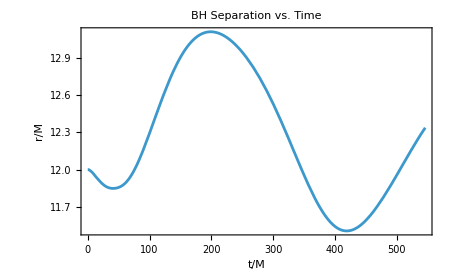
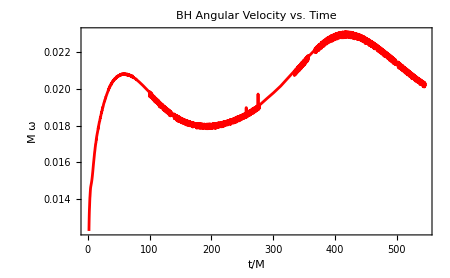

```mathematica
(*Plot the binary separation and angular velocity with time*)
Row[{Show[Plot[isep[t],{t,tMIN,tMAX},PlotStyle->RGBColor[61/255,153/255,204/255]],Frame->True,FrameLabel->{"t/M","r/M"},ImageSize->450,PlotLabel->"BH Separation vs. Time"],Show[Plot[iωET[t],{t,tMIN,tMAX},PlotStyle->Red],Frame->True,FrameLabel->{"t/M","M ω"},ImageSize->450,PlotLabel->"BH Angular Velocity vs. Time"]},"          "]
(*TODO: Could be helpful to add vertical indicators of merger and the ISCO which help set MaxTime in the fitting function below*)
```

## Fit Waveform

Time Domain: {0.,335.897}

Initial Separation R_0: 12.

Initial Orbital Frequency Ω_0: 0.0215083

Initial Orbital Period T_0: 292.128

{ER`e→0.00139277,ER`a→0.888818,ER`t0→-4.98129,ER`ω1→0.711429,ER`t1→6.28319,ke→-9.92567,kω→-3.48583×10^-9}

Eccentricity Estimate from Ω:
0.0323774 (1-0.000992567 T)
±23.2468 (0.0791836 Abs[1-0.000992567 T]+0.000491545 Abs[T])

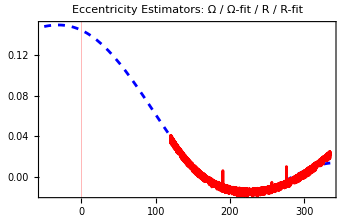
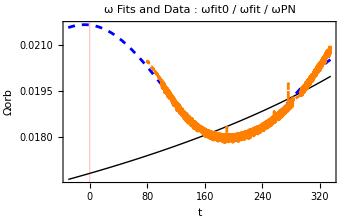
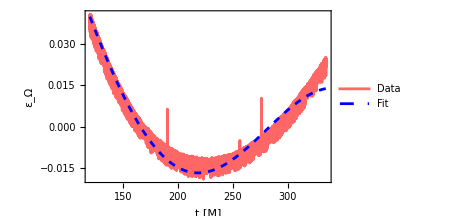

```mathematica
(*going from 120 to tMAX on q1_r12_s0_max15_e0, ecc=0.0431921321289*)
eccIterDE=myEstimateEccentricityReductionPN35D10DE[eta,χ1,χ2,seplist[[1]],ωlist[[1]],"MinTime"->120,"MaxTime"->tMAX]//Quiet;
(*TODO: Maybe save these plots to the directory and also compute helpful things like Subscript[e, Ω,max] to measure improvement*)
(*I think if I want to plot multiple iterations then I will need to save ωfitpars somewhere*)
```

## Compute Correction Factors

```mathematica
sign=-1;
eccT0=eccIterDE/.T->0;
eΩT0=eccT0[[1]];δeΩT0=eccT0[[2]];
ϕT0=eccT0[[3]];δϕT0=eccT0[[4]];
AmpT0=eccT0[[5]];δAmpT0=eccT0[[6]];
λr1pnRes=1/λr1PNResSum[AmpT0,ϕT0,Pr35PN[dist,q0,χ1,χ2,1],mωr35SPN[dist,q0,χ1,χ2,1],dist,eta,1]; (* Eq. (3.47) of the paper *)
λt1pnRes=1/λt1PNResSum[AmpT0,ϕT0,mωr35SPN[dist,q0,χ1,χ2,1],dist,eta,1]; (* Eq. (3.46) of the paper *)
λt1pn =λt1PNLin[Abs@eΩT0,sign,dist,eta]; (* Eq. (3.25) of the paper *)
δR=δrmas[AmpT0,dist,mωr35SPN[dist,q0,χ1,χ2,1],q0,1]; (* Eq. (3.57) of the paper *)

Print[StringJoin[
"λ_(r1, PN Res) = ",ToString[λr1pnRes],"\n",
"λ_(t1, PN Res) = ",ToString[λt1pnRes],"\n",
"λ_(t1, PN) = ",ToString[λt1pn],"\n",
"δ_r = ",ToString[δR]
]]
```

λ_(r1, PN Res) = -0.461183
λ_(t1, PN Res) = 0.983441
λ_(t1, PN) = 0.982422
δ_r = 0.307501

## Corrected Initial Data

```mathematica
r0=Norm[pos1-pos2]
r1=r0+δR; (*Eq. 3.50*)
pt0=p1[[2]];
(*NOTE: These are assuming the BHs are on the x-axis so that the y-component of the momentum is tangential and the x-component of the momentum is radial*)
pt1=λt1pnRes*pt0; (*Eq 3.23*)
(*NOTE: We use λr1pnRes and not λr1pn for reasons I don't entirely understand*)
pr0=p1[[1]];
pr1=λr1pnRes*pr0; (*Eq 3.23*)
```

12.

```mathematica
(*Compute the new initial data based on correction factors*)
mass1=mass1;
mass2=mass2;
pos1={r1/2,0.0,0.0};
pos2={-r1/2,0.0,0.0};
p1={pr1,pt1,0.0};
p2={-pr1,-pt1,0.0};
χ1=χ1;
χ2=χ2;

(*Print Dendro par file formatted initial data*)
(*NOTE: I need to work something out to make it output a zero after the decimal place if there isn't one, but for now that can easily be added manually*)
(*NOTE: There are also issues when there are exponents. I just need to find a better string form*)
Print["Corrected Initial Data:"]
Print[StringJoin[
"BSSN_BH1 = { MASS = ",ToString[mass1],", X = ",ToString[pos1[[1]]],", Y = ",ToString[pos1[[2]]],", Z = ",ToString[pos1[[3]]],", V_X = ",ToString[p1[[1]]],", V_Y = ",ToString[p1[[2]]],", V_Z = ",ToString[p1[[3]]],", SPIN = ",ToString[χ1[[1]]],", SPIN_THETA = ",ToString[χ1[[2]]],", SPIN_PHI = ",ToString[χ1[[3]]]," }"
]]
Print[StringJoin[
"BSSN_BH2 = { MASS = ",ToString[mass2],", X = ",ToString[pos2[[1]]],", Y = ",ToString[pos2[[2]]],", Z = ",ToString[pos2[[3]]],", V_X = ",ToString[p2[[1]]],", V_Y = ",ToString[p2[[2]]],", V_Z = ",ToString[p2[[3]]],", SPIN = ",ToString[χ2[[1]]],", SPIN_THETA = ",ToString[χ2[[2]]],", SPIN_PHI = ",ToString[χ2[[3]]]," }"
]]
```

Corrected Initial Data:

BSSN_BH1 = { MASS = 0.4824, X = 6.15375, Y = 0., Z = 0., V_X = 0.000248268, V_Y = 0.083685, V_Z = 0., SPIN = 0., SPIN_THETA = 0., SPIN_PHI = 0. }

BSSN_BH2 = { MASS = 0.4824, X = -6.15375, Y = 0., Z = 0., V_X = -0.000248268, V_Y = -0.083685, V_Z = 0., SPIN = 0., SPIN_THETA = 0., SPIN_PHI = 0. }